# SurfCalc 14 for e2V vendor-supplied pre-ship data files

Version notes

2016.05.27 - Cleaned up filename
2015.12.28 - v03 - Fixed stats report output format. Cleaned up extraneous cells. Optimized for no LSF detrend.
2015.08.20 - v02 - Added readin formats for both e2V data files: .XLS and .csv. The XLS data is in a 2D array; the csv data is in a list. Need to convert the 2D data into a list by binning up to 1mm size pixels and then flattening. The 2D data goes thru the array analysis, but both types of data then go through the FREEFORM analysis. 
2015.07.14 - Added ITL VIEW data format read in.

Derived from SurfAnal 13 freeform cloud.nb

This notebook handles both types of data files delivered by e2V: a list of XYZ triplets from the CT100 machine, and an Excel .XLS spreadsheet file for the Wyko interferometer.

Need to strip off the z values and do statistics on them, keeping track of what x-y coord is of each z-value. THis is done by partitioning appropriately at the right time in the analysis.

Execute next statement first. It causes all of the initialization cells to be executed.

## 1. Initialize

Reset the kernal when starting

```mathematica
<<Utilities`CleanSlate`;
```

```mathematica
CleanSlate[]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 44593 Kb

{Utilities`CleanSlate`,WolframAlphaClient`,Utilities`URLTools`,JLink`,ComputationalGeometry`,StreamingLoader`,IconizeLoader`,CloudObjectLoader`,PacletManager`,System`,Global`}

Data and time of last saved modification. This is an Initialization cell that executes automatically whenever the nb is opened.

```mathematica
nb=EvaluationNotebook[]
```

2azi5_shm11FrontEndObject[LinkObject["2azi5_shm", 3, 1]]11SurfCalc14_e2V_vendor_data_analysis_v04.nb/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/_Analysis codes/Vendor Metrology-data-analysis/SurfCalc14_e2V_vendor_data_analysis_v04.nb

```mathematica
DateString["FileModificationTime"/.NotebookInformation[],TimeZone->-10]
```

Fri 27 May 2016 09:36:27

```mathematica
Off[General::"spell1"]
(*<<"BarCharts`";<<"Histograms`";<<"PieCharts`"
<<"LinearRegression`"*)
```

```mathematica
<<ComputationalGeometry`
```

```mathematica
$SystemID
```

MacOSX-x86-64

```mathematica
$OperatingSystem
```

MacOSX

Use the file path separator form appropriate for the computer platform,  MacOSX or Windows&Linux

```mathematica
If[$OperatingSystem=="MacOSX",sep$="/",sep$="\\"];
```

```mathematica
sep$
```

/

```mathematica
SetOptions[ListPlot3D,BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->10]];
```

```mathematica
SetOptions[Histogram,BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->10]];
```

```mathematica
SetOptions[ListPointPlot3D,BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->10]];
```

```mathematica
SetOptions[ListContourPlot,BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->10]];
```

```mathematica
SetOptions[Histogram,BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->10]];
```

#### Conversion factors to meters for numbers in the indicated units:

```mathematica
mm=10.^-3;
micron=10.^-6;
µm=10.^-6;
nm=10.^-9;
Angstroms=10.^-10;
micronsToAngstroms=10^4;
```

```mathematica
filename=.;filenamefull=.;fnames=.;plotname=.;filepath=.;filepathfull=.;filein=.;fileinroot=.;fileinS=.;workpath=.;infiledir=.;workdir=.;
```

```mathematica
autoOutput=True
```

True

## 2. Define statistical functions for profile data.

MAKE SURE THE FOURIER OPTIONS ARE SET CORRECTLY EACH TIME THE FT IS DONE.

Define the biased stddev functiion. The built in StdDev fcn has n-1 in the denom. Change it to n.

Now compute std dev in different ways: The default StandardDeviation is the unbiased version, with n-1 in the denominator.

```mathematica
sdevBiased=.
```

```mathematica
sdevUnB[in_]:=N[StandardDeviation[in]]
```

```mathematica
sdevBiased[in_]:=StandardDeviation[in]Sqrt[(Length[in]-1)/Length[in]]
```

```mathematica
rmsBias[in_]:=Sqrt[Plus@@(in^2)/Length[in]]
```

Next is the RMS. Sum the squares, divide by N and then take the root. (Root of the Mean Square)

```mathematica
rmsrawbiased=.;
```

```mathematica
rms[in_]:=N[√((Plus@@((in)^2))/Length[in])]
```

See that one must subtract the mean from the input data first, before squaring, in order to compute the standard deviation correctly.

```mathematica
sdevBruteUnBiased[in_]:=N[√((Plus@@((in-Mean[in])^2))/(Length[in]-1))]
```

```mathematica
detrend[anylist_,order_Integer]:=Block[{npts,xlist,fitlist,x},
If[
order>=0,
xlist=Table[x^i,{i,0,order}];
		npts=Length[anylist];
		func=Fit[anylist,xlist,x];
		fitlist={};
		Do[AppendTo[fitlist,func],{x,1,npts}];
		Return[anylist-fitlist],
Return[anylist]
]
]
```

#### Define a RMS function to compute rms from PSD data. Input arguments are: psd=name of PSD list; ntot=total points in source profile; delx= physical increment value for each data point step; lo and hi = index value in the PSD list.

```mathematica
psd1[in_,delx_]:=(SetOptions[Fourier,FourierParameters->{1,1}];
nPts=Length[in];
FTwork=Fourier[in];
psd2side=(2 delx/nPts) Abs[FTwork]^2;
psd1side=Drop[psd2side,-Floor[(nPts-1)/2]];
(*Apply bookkeeping factors to end terms*)
psd1side[[1]]=psd1side[[1]]/2; 
If[EvenQ[nPts],psd1side[[-1]]=psd1side[[-1]]/2,Null];
psd1side
)
```

```mathematica
npts=.
```

```mathematica
test11={1,2,3,4,5,6,7,8,9,10,11};
```

```mathematica
psd1[test11,1.]
```

{396.,69.2929,18.8168,9.62957,6.64709,5.6137}

```mathematica
nPts
```

11

```mathematica
Length[psd2side]
```

11

#### Define a RMS function to compute rms from PSD data. Input arguments are: psd=name of PSD list; ntot=total points in source profile; delx= physical increment value for each data point step; lo and hi = index value in the PSD list. NOTE: Need to know the length of the input z-vector for the ntot number. Can't get it from the length of the psd list. It should be the length of the psd2side list if this corresponds to the input psd list.

```mathematica
rmspsdIDX[psd_,nztot_,delx_,lo_,hi_]:=(rmsval=N[√((Plus@@Take[psd,{lo,hi}])/(nztot delx))];Print["RMS over index range [",lo,",",hi,"] = ",rmsval])
```

```mathematica
rmspsd[psd_,nztot_,delx_,lo_,hi_]:=N[√((Plus@@Take[psd,{lo,hi}])/(nztot delx))];
```

Now generalize the variance calculation to apply to zero-padded data to give the same result as for the original data set. Need to boost up each term separately.

```mathematica
varGen[anylist_,beforeLen_,afterLen_]:=N[sfac=afterLen/beforeLen;(sfac Plus@@(anylist^2))/afterLen-sfac^2 ((Plus@@anylist)/afterLen)^2]
```

```mathematica
sdevGen=√varGen[worklist,nbefore,nafter]
```

{√(-(3.69734×10^9)/nbefore^2+(2.97839×10^6)/nbefore),√(-(3.69304×10^9)/nbefore^2+(2.97588×10^6)/nbefore),√(-21750.9/nbefore^2+335.495/nbefore)}

#### Add a point digitizer to a plot. Results are put into vector "res".

```mathematica
locatePts[plotname_]:=
Block[ {}, 
res = {}; 
Dynamic[res]; 
  EventHandler[ 
         plotname, {"MouseDown" :>( AppendTo[res, MousePosition["Graphics"]])} 
        ] ]
```

#### The following tick function rescales the axes labels from the default [xmin, xmax] range by offsetting the starting point by b and scaling the tick value by m. Note that you need to specify the AxesOrigin in terms of the unshifted function.

```mathematica
$TextStyle={FontFamily->Arial,FontSize->10}
```

{FontFamily→Arial,FontSize→10}

```mathematica
Style[PlotLabel,DefaultOptions->{FontFamily->Arial}]
```

PlotLabel

```mathematica
tickf[min_,max_,m_,b_,step_]:= Table[{i,m (i-b)},{i,min,max,step}]
```

## 2.1 Define statistical functions for 2 D areal data

```mathematica
mean2D[array_]:=Total[array,2]/Apply[Times,Dimensions[array]]//N
```

```mathematica
sumsq2D[array_]:=Total[array^2,2]
```

```mathematica
meansq2D[array_]:=Total[array^2,2]/Apply[Times,Dimensions[array]]//N
```

```mathematica
(*meansq2D[array_]:=1/(Length[array]  Length[array[[1]]]) Total[array^2,2]//N*)
```

```mathematica
rms2D[array_]:=Sqrt[meansq2D[array]]
```

## 3.0 Insert full file path here to set working directory:

```mathematica
(*"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/_ITL pending/Pre First Art mech sample data/VIEW_sn19197.txt";*)
```

Set default

```mathematica
filepathfull = Input["Input file path to the desired data file",filepathfull]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/_Production DATA/e2V prod sensors/e2V-114/15433-03-01_Pkg114_-100C_WYKO_cold_flatness.csv

```mathematica
infiledir=DirectoryName[filepathfull]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/_Production DATA/e2V prod sensors/e2V-114/

```mathematica
SetDirectory[infiledir]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/_Production DATA/e2V prod sensors/e2V-114

```mathematica
SelectionMove[nb,Next,Cell]
```

## 3.1 Pick one data input section. 2015.07.13

Result of data entry should be urdataS array of triplets.

### 3.1.2 Read format for e2V xls height data file

```mathematica
Directory[]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/_Production DATA/e2V prod sensors/e2V-107

```mathematica
fnames=FileNames[{"*.XLS*","*.CSV"}]
```

{15433-03-04_Pkg107_100C_WYKO_cold_flatness.xls,15433-03-04_Pkg107_Die_Alignment_Check.xls,15433-03-04_Pkg107_Mechanical_Shim_Test_Sheet.xls,15433-03-04_Pkg107_RT_CT100_flatness.csv,15433-03-04_Pkg107_Support_Alignment_Check.xls}

```mathematica
Length[fnames]
```

5

```mathematica
Table[{i,fnames[[i]]},{i,Length[fnames]}]//TableForm
```

1 | 15433-03-04_Pkg107_100C_WYKO_cold_flatness.xls
2 | 15433-03-04_Pkg107_Die_Alignment_Check.xls
3 | 15433-03-04_Pkg107_Mechanical_Shim_Test_Sheet.xls
4 | 15433-03-04_Pkg107_RT_CT100_flatness.csv
5 | 15433-03-04_Pkg107_Support_Alignment_Check.xls

```mathematica
nf=Input["Enter index of file desired",nf]
```

1

```mathematica
filein=fnames[[nf]]
```

15433-03-04_Pkg107_100C_WYKO_cold_flatness.xls

```mathematica
fileinroot=FileBaseName[filein]
```

15433-03-04_Pkg107_100C_WYKO_cold_flatness

```mathematica
xunit$=yunit$="mm";
```

```mathematica
zunit$="µm";
```

Input the full file

```mathematica
rawdata=Import[filein,{"Data",1}];
```

```mathematica
(*rawdata=Import[filein,"Data"];*)
```

```mathematica
Length[rawdata]
```

0

```mathematica
rawdata[[11]]
```

xsize: 243⟦11⟧

Extract the header lines. Define function getnum[] to extract the numbers for selected items. Only works for numbers.

```mathematica
header=Take[rawdata,12];
```

```mathematica
header2=Take[header[[All,1]]]
```

Take[xsize: 243,12]⟦All,1⟧

```mathematica
getnum[headlist_,item$_]:=Module[{postpix,xlin,xpix$},
posxpix=Position[StringContainsQ[headlist,item$],True];
xlin=Extract[headlist,posxpix][[1]];
xpix$=ReadList[StringToStream[xlin],Word,WordSeparators->{":"}][[2]];
ToExpression[xpix$]
]
```

```mathematica
xpix=getnum[header2,"xpix"]
```

Word

```mathematica
pixsize=xpix*1000  (*mm*)
```

1000 Word

Now work on data array

```mathematica
raw=Drop[rawdata,12];
```

```mathematica
Length[raw]
```

2

```mathematica
ArrayPlot[raw,ImageSize->200]
```

ArrayPlot[Drop[xsize: 243,12],ImageSize→200]

```mathematica
NumberQ[raw[[100,50]]]
```

False

```mathematica
raw[[100,51]]
```

Drop[xsize: 243,12]⟦100,51⟧

```mathematica
Length[raw]
```

2

Open stream file for input.

```mathematica
Dimensions[raw]
```

{2}

Now read in the header records which are terminated by the record separator specified above. This set the pointer to the first valid data number.

```mathematica
rawtrim=Reap[
Do[If[NumberQ[raw[[i,50]]],Sow[raw[[i]]]]
,{i,1,Length[raw]}]]//Drop[#,1]&;
```

```mathematica
rawtrim=rawtrim//Flatten[#,2]&
```

{}

Extract rows that have numbers

```mathematica
(*rawtrim=Flatten[rawtrim,2];*)
```

```mathematica
ArrayPlot[rawtrim,ImageSize->200]
```

-Graphics-

```mathematica
raw2=Transpose[rawtrim];
```

```mathematica
rawtrim2=Reap[
Do[If[NumberQ[raw2[[i,50]]],Sow[raw2[[i]]]]
,{i,1,Length[raw2]}]]//Drop[#,1]&;
rawtrim2=Flatten[rawtrim2,2]//Transpose;
```

```mathematica
ArrayPlot[rawtrim2,ImageSize->200,ColorFunction->"Rainbow"]
```

ArrayPlot[Transpose[{}],ImageSize→200,ColorFunction→Rainbow]

```mathematica
Dimensions[rawtrim2]
```

{1}

Find the NaN points defined by “--“ and replace with 0.0

```mathematica
bdpts=Position[rawtrim2,"--"]
```

{}

```mathematica
bdpts[[1]]
```

{}⟦1⟧

```mathematica
rawtrim2=
ReplacePart[rawtrim2,bdpts->0.0];
```

```mathematica
{nRows,nCols}=Dimensions[rawtrim2]
```

{1}

```mathematica
bigData=rawtrim2;
```

```mathematica
urdataS=bigData;
```

```mathematica
worksurf=bigData;
```

```mathematica
Dimensions[worksurf]
```

{1}

Set flag to delete bad points or just set them to zero.

```mathematica
Mean[Mean[bigData]]
```

Mean[Mean[Transpose[{}]]]

Now bin the data points into larger evvective pixels.

```mathematica
SelectionMove[nb,After,Cell]
```

### 3.1.3 Read format for e2V csv WYKO height data file 2016.05.27

```mathematica
Directory[]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/_Production DATA/e2V prod sensors/e2V-114

```mathematica
fnames=FileNames[{"*.XLS*","*.CSV"}]
```

{15433-03-01_Pkg114_-100C_WYKO_cold_flatness.csv,15433-03-01_Pkg114_Mechanical_Shim_Test_Sheet.xls,15433-03-01_Pkg114_RT_CT100_flatness.csv,15433-03-01_Pkg114_Support_Algnment_Check.xls}

```mathematica
Length[fnames]
```

4

```mathematica
Table[{i,fnames[[i]]},{i,Length[fnames]}]//TableForm
```

1 | 15433-03-01_Pkg114_-100C_WYKO_cold_flatness.csv
2 | 15433-03-01_Pkg114_Mechanical_Shim_Test_Sheet.xls
3 | 15433-03-01_Pkg114_RT_CT100_flatness.csv
4 | 15433-03-01_Pkg114_Support_Algnment_Check.xls

```mathematica
nf=Input["Enter index of file desired",nf]
```

1

```mathematica
filein=fnames[[nf]]
```

15433-03-01_Pkg114_-100C_WYKO_cold_flatness.csv

```mathematica
fileinroot=FileBaseName[filein]
```

15433-03-01_Pkg114_-100C_WYKO_cold_flatness

```mathematica
xunit$=yunit$="mm";
```

```mathematica
zunit$="µm";
```

Input the full file

```mathematica
rawdata=Import[filein,{"Data",1}];
```

```mathematica
rawdata=Import[filein,"Data"];
```

```mathematica
rawdata
```

{{xsize: 243},330,{--,--,--,--,--,--,--,--,--,--,--,--,--,--,--,--,--,--,--,--,--,--,--,--,--,--,--,--,--,--,--,--,--,178,--,--,--,--,--,--,--,--,--,--,--,--,--,--,--,--,--,--,--,--,--,--,--,--,--,--,--,--,--,--,--,--,}}
 |  |  |  |

```mathematica
Length[rawdata]
```

332

```mathematica
rawdata[[11]]
```

{delimiter: csv}

Extract the header lines. Define function getnum[] to extract the numbers for selected items. Only works for numbers.

```mathematica
header=Take[rawdata,12];
```

```mathematica
header2=Take[header[[All,1]]]
```

{xsize: 243,ysize: 320,type: phase,badpixel: --,date: Tue May 17 07:38:07 2016,title: 15433-03-01 cold ,wavelength: 632.80000,wedge: 0.50000,xpix: 0.000442030674594,aspect: 1.00000,delimiter: csv,}

```mathematica
getnum[headlist_,item$_]:=Module[{postpix,xlin,xpix$},
posxpix=Position[StringContainsQ[headlist,item$],True];
xlin=Extract[headlist,posxpix][[1]];
xpix$=ReadList[StringToStream[xlin],Word,WordSeparators->{":"}][[2]];
ToExpression[xpix$]
]
```

```mathematica
xpix=getnum[header2,"xpix"]
```

0.000442031

```mathematica
pixsize=xpix*1000  (*mm*)
```

0.442031

Now work on data array

```mathematica
raw=Drop[rawdata,12];
```

```mathematica
Length[raw]
```

320

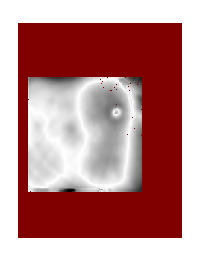

```mathematica
ArrayPlot[raw,ImageSize->200]
```

```mathematica
NumberQ[raw[[100,50]]]
```

True

```mathematica
raw[[100,51]]
```

-0.35874

```mathematica
Length[raw]
```

320

Open stream file for input.

```mathematica
Dimensions[raw]
```

{320,244}

Now read in the header records which are terminated by the record separator specified above. This set the pointer to the first valid data number.

```mathematica
rawtrim=Reap[
Do[If[NumberQ[raw[[i,50]]],Sow[raw[[i]]]]
,{i,1,Length[raw]}]]//Drop[#,1]&;
```

```mathematica
rawtrim=rawtrim//Flatten[#,2]&
```

{1}
 |  |  |  |

Extract rows that have numbers

```mathematica
(*rawtrim=Flatten[rawtrim,2];*)
```

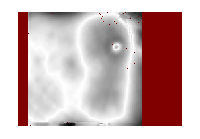

```mathematica
ArrayPlot[rawtrim,ImageSize->200]
```

```mathematica
raw2=Transpose[rawtrim];
```

```mathematica
rawtrim2=Reap[
Do[If[NumberQ[raw2[[i,50]]],Sow[raw2[[i]]]]
,{i,1,Length[raw2]}]]//Drop[#,1]&;
rawtrim2=Flatten[rawtrim2,2]//Transpose;
```

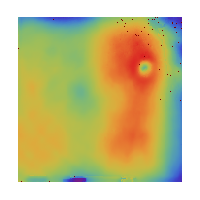

```mathematica
ArrayPlot[rawtrim2,ImageSize->200,ColorFunction->"Rainbow"]
```

```mathematica
Dimensions[rawtrim2]
```

{170,169}

Find the NaN points defined by “--“ and replace with 0.0

```mathematica
bdpts=Position[rawtrim2,"--"]
```

{{1,119},{1,142},{1,144},{2,152},{3,37},{3,107},{3,118},{3,135},{3,139},{3,141},{4,108},{6,103},{6,145},{6,160},{6,169},{7,111},{7,135},{7,160},{7,164},{10,110},{10,152},{11,131},{11,162},{11,163},{12,169},{13,139},{14,149},{15,113},{15,128},{16,164},{18,131},{18,135},{18,163},{19,122},{19,135},{20,123},{20,125},{20,150},{27,166},{29,135},{30,148},{31,160},{33,1},{41,131},{48,168},{49,126},{52,129},{55,146},{57,166},{60,155},{61,158},{77,158},{85,147},{87,168},{165,59},{170,4},{170,33}}

```mathematica
bdpts[[1]]
```

{1,119}

```mathematica
rawtrim2=
ReplacePart[rawtrim2,bdpts->0.0];
```

```mathematica
{nRows,nCols}=Dimensions[rawtrim2]
```

{170,169}

```mathematica
bigData=rawtrim2;
```

```mathematica
urdataS=bigData;
```

```mathematica
worksurf=bigData;
```

```mathematica
Dimensions[worksurf]
```

{170,169}

Set flag to delete bad points or just set them to zero.

```mathematica
Mean[Mean[bigData]]
```

0.000446253

```mathematica
SelectionMove[nb,Before,Cell]
```

### 3.1.4 Read format for e2V csv file from CT100 machine.

```mathematica
Directory[]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/_Production DATA/e2V prod sensors/e2V-114

```mathematica
fnames=FileNames["*.csv*"];
```

```mathematica
Length[fnames]
```

2

```mathematica
Table[{i,fnames[[i]]},{i,Length[fnames]}]//TableForm
```

1 | 15433-03-01_Pkg114_-100C_WYKO_cold_flatness.csv
2 | 15433-03-01_Pkg114_RT_CT100_flatness.csv

```mathematica
nf=Input["Enter index of file desired",nf]
```

2

```mathematica
filein=fnames[[nf]]
```

15433-03-01_Pkg114_RT_CT100_flatness.csv

```mathematica
fileinroot=FileBaseName[filein]
```

15433-03-01_Pkg114_RT_CT100_flatness

```mathematica
zunit$="µm";
```

Input the full file

```mathematica
(*ResetDirectory[]*)
```

```mathematica
rawdataUr=Import[filein,"Data"];
```

```mathematica
Length[rawdataUr]
```

30503

```mathematica
rawdataUr[[1;;10]]
```

{{51.149,60.967,-0.0000976},{51.629,60.967,0.0000353},{52.109,60.967,-0.0000354},{52.589,60.967,-0.0000445},{53.069,60.967,-0.0000445},{53.549,60.967,-0.0000926},{54.029,60.967,-0.0000217},{54.509,60.967,0.0001624},{54.989,60.967,0.0000605},{55.229,60.967,0.0000684}}

#### Execute one of these expressions to convert data units to [mm,mm,µm] NOT FOR WYKO 2D ARRAY DATA

Need to convert data units to X[mm], Y[mm], Z[microns]

For input as [µm,µm,µm]:

```mathematica
rawdata=Map[MapAt[Times[#,10.^-3]&,#,{{1},{2}}]&,rawdataUr];
```

For input as X[mm], Y[mm], Z[mm]:

```mathematica
rawdata=Map[MapAt[Times[#,10.^3]&,#,{{3}}]&,rawdataUr];
```

#### End of selections. Continue from here

```mathematica
xunit$=yunit$="mm";zunit$="µm";
```

```mathematica
urdataS=rawdata;
worklist=rawdata;
datain3=rawdata;
```

```mathematica
worklist[[1;;3]]
```

{{xsize: 243},{ysize: 320},{type: phase}}

## 2.9 Create subdir for data file output

```mathematica
fileinroot
```

15433-03-01_Pkg114_-100C_WYKO_cold_flatness

```mathematica
fileinS=StringReplace[fileinroot," "->"_"]
```

15433-03-01_Pkg114_-100C_WYKO_cold_flatness

```mathematica
Directory[]  (* This is the current default directory *)
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/_Production DATA/e2V prod sensors/e2V-114

```mathematica
workdir=fileinroot<>"_files"
```

15433-03-01_Pkg114_-100C_WYKO_cold_flatness_files

```mathematica
DirectoryQ[workdir]
```

False

```mathematica
If[!DirectoryQ[workdir],CreateDirectory[workdir];Print["New work dir created"],Print[workdir<>" already exists. Using it for output."]]
```

New work dir created

```mathematica
SetDirectory[workdir]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/_Production DATA/e2V prod sensors/e2V-114/15433-03-01_Pkg114_-100C_WYKO_cold_flatness_files

### 3.1) No REF correction needed

```mathematica
fitidxR$="0,0"  (* Default string for no REF corrections *)
```

0,0

```mathematica
nfRef=0;
```

```mathematica
fileinS
```

15433-03-01_Pkg114_-100C_WYKO_cold_flatness

```mathematica
urdataSR=urdataS; (* No REF. Copy surface into SR array. *)
```

```mathematica
Length[urdataSR]
```

170

```mathematica
SelectionMove[nb,Next,Cell,2]
```

```mathematica
NotebookLocate["iterate after outlier removal"]
```

## 4.0 Extract subregion from 2D bigData2Dz and change nrows and ncols accordingly. Required for Wyko csv xls files but NOT for CT100 files.

```mathematica
Print["Abort to avoid unwanted calcs in this section."];Interrupt[](* Abort the calc if the outer cell is executed *)
```

Abort to avoid unwanted calcs in this section.

#### Execute these cells in groups, not all at once.

```mathematica
{nRows,nCols}
```

{170,169}

```mathematica
nPts=nRows nCols
```

28730

Set the initial values of the internal variables outside the Manipulate, otherwise hang occurs.

```mathematica
{{rtop,rbot},{cleft,cright}}={{1,nRows},{1,nCols}}
```

{{1,170},{1,169}}

```mathematica
datainXYZSR=urdataSR;
```

```mathematica
skipnum;
```

```mathematica
ListPointPlot3D[Take[datainXYZSR,{1,-1}],ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
(*Manipulate[ListPointPlot3D[Take[datainXYZSR,i]],{i,1,nRows*nCols,1},SaveDefinitions->True]*)
```

Extract the z-val from the flattened list, then repartition into a 2D array.

```mathematica
datainXYZSR[[1,1]]
```

-0.61727

```mathematica
bigdataz=datainXYZSR;
```

```mathematica
Length[bigdataz]
```

170

```mathematica
Dimensions[bigdataz]
```

{170,169}

```mathematica
{Min[bigdataz],Max[bigdataz]}
```

{-1.62367,0.91555}

```mathematica
bigdataz[[1,1]]
```

-0.61727

```mathematica
nRows
```

170

```mathematica
rmin=1;rmax=Min[nRows,256];cleft=1;cright=Min[256,nCols];
```

```mathematica
{{rmin,rmax},{cleft,cright}}
```

{{1,170},{1,169}}

```mathematica
Manipulate[ReliefPlot[Take[bigdataz ,{rmin,rmax},{cleft,cright}] ,AspectRatio->1.0,ColorFunction->"Rainbow",DataReversed->True,FrameTicks->{Table[{u-rmin,u},{u,rmin,rmax,(rmax-rmin)/5//Floor}],Table[{v-cleft,v},{v,cleft,cright,(cright-cleft)/6//Floor}]}],
{rmin,1,rmax-2,1,Appearance->"Open"},{rmax,rmin,nRows,1,Appearance->"Open"},{cleft,1,cright-1,1,Appearance->"Open"},{cright,cleft+2,nCols,1,Appearance->"Open"},LocalizeVariables->False]
```

```mathematica
{{rtop,rbot},{cleft,cright}}={{rmin,rmax},{cleft,cright}}
```

{{1,170},{1,169}}

### Execute this next when region within bigData is defined. This defines subarray bigdata. Start here to reset the bigdata array when re-binning the original array.

```mathematica
bigdata=Take[bigdataz ,{rtop,rbot},{cleft,cright}];
```

```mathematica
nrows=Length[bigdata]
```

170

```mathematica
ncols=Length[bigdata[[1]]]
```

169

```mathematica
npts=ntot2Dpts=ncols nrows
```

28730

```mathematica
delx=pixsize
```

0.442031

Now bin the pixels into larger size

```mathematica
Dimensions[bigdata]
```

{170,169}

```mathematica
pixbinx=pixbiny=1
```

1

```mathematica
dely=delx
```

0.442031

```mathematica
rbin=1;
```

```mathematica
cbin=1;
```

```mathematica
{rbin,cbin}=Input["Set desired vertical row and horizontal col pixel binning. {rows,cols}.",{rbin,cbin}]
```

{4,4}

```mathematica
{pixbinrows=rbin,pixbincols=cbin}
```

{4,4}

```mathematica
rbin$=ToString[rbin]
```

4

Only execute this once after reading in the data file.

```mathematica
{delx=pixbincols delx,dely=pixbinrows dely}
```

{1.76812,1.76812}

```mathematica
Dimensions[bigdata]
```

{170,169}

```mathematica
bigdata2=Partition[bigdata,{pixbinrows,pixbincols}];
```

```mathematica
Dimensions[bigdata2]
```

{42,42,4,4}

This is one pixel:

```mathematica
(* ArrayPlot[bigdata2[[1,1]],ColorFunction->"Rainbow",AspectRatio->1] *)
```

Now compute the mean within each pixel. Create binned pixel array mb.

```mathematica
mb=Map[Mean,Map[Mean,bigdata2,{3}],{2}];
```

```mathematica
Dimensions[mb]
```

{42,42}

```mathematica
StandardDeviation[mb//Flatten]
```

0.422787

Check that partitioning and binning gives desired result

```mathematica
Dimensions[bigdata2]
```

{42,42,4,4}

```mathematica
Mean[bigdata[[1;;4,1;;4]]]
```

{-0.708805,-0.807897,-0.862972,-0.882255}

```mathematica
bigdata2[[1,1]]
```

{{-0.61727,-0.86412,-0.89554,-0.90156},{-0.72683,-0.81401,-0.87062,-0.89618},{-0.76998,-0.79807,-0.8582,-0.88523},{-0.72114,-0.75539,-0.82753,-0.84605}}

```mathematica
Mean[bigdata2[[1,1]]]//Mean
```

-0.815482

```mathematica
mb[[1,1]]
```

-0.815483

All looks OK. Use mb array

```mathematica
nrows=Dimensions[mb][[1]]
ncols=Dimensions[mb][[2]]
npts=nrows ncols
```

42

42

1764

```mathematica
rms2D[mb]
```

0.422897

```mathematica
hrange[binlist_,min_,max_]:=Quantile[binlist,{min,max}];
```

```mathematica
stats[zarray2D_]:=
Module[{},
ar=zarray2D//Flatten;
maxzF=Max[ar];minzF=Min[ar];sigmaF=StandardDeviation[ar];
hgtrangeF95=hrange[ar,0.025,0.975];
PVrangeF95=hgtrangeF95[[2]]-hgtrangeF95[[1]];
hgtrangeF99=hrange[ar,0.005,0.995];PVrangeF99=hgtrangeF99[[2]]-hgtrangeF99[[1]];
sigmaF//NumberForm[#,5]&
]
```

```mathematica
stats[mb]
```

0.42279

```mathematica
titles={maxzF,minzF,sigmaF,
hgtrangeF95,
PVrangeF95,
hgtrangeF99,PVrangeF99,
sigmaF}//HoldForm//ToString//StringTake[#,{2,-2}]&
```

maxzF, minzF, sigmaF, hgtrangeF95, PVrangeF95, hgtrangeF99, PVrangeF99, sigmaF

```mathematica
t2=StringSplit[titles,","]//Flatten
```

{maxzF, minzF, sigmaF, hgtrangeF95, PVrangeF95, hgtrangeF99, PVrangeF99, sigmaF}

```mathematica
reslist={maxzF,minzF,sigmaF,hgtrangeF95,PVrangeF95,hgtrangeF99,PVrangeF99,sigmaF}
```

{0.880575,-1.38469,0.422787,{-0.937903,0.742606},1.68051,{-1.21765,0.840877},2.05853,0.422787}

```mathematica
restable={t2,reslist}//Transpose
```

{{maxzF,0.880575},{ minzF,-1.38469},{ sigmaF,0.422787},{ hgtrangeF95,{-0.937903,0.742606}},{ PVrangeF95,1.68051},{ hgtrangeF99,{-1.21765,0.840877}},{ PVrangeF99,2.05853},{ sigmaF,0.422787}}

```mathematica
restableT=restable
```

{{maxzF,0.880575},{ minzF,-1.38469},{ sigmaF,0.422787},{ hgtrangeF95,{-0.937903,0.742606}},{ PVrangeF95,1.68051},{ hgtrangeF99,{-1.21765,0.840877}},{ PVrangeF99,2.05853},{ sigmaF,0.422787}}

```mathematica
quantlist=Reverse[{0.0,0.005,0.01,0.025,0.25,0.50,0.75,0.975,0.99,0.995,1.0}];
```

```mathematica
qresF=Quantile[mb//Flatten,quantlist];
```

```mathematica
Transpose[{quantlist,qresF}]
```

{{1.,0.880575},{0.995,0.840877},{0.99,0.814426},{0.975,0.742606},{0.75,0.281134},{0.5,0.0274281},{0.25,-0.241218},{0.025,-0.937903},{0.01,-1.12297},{0.005,-1.21765},{0.,-1.38469}}

```mathematica
qtableF=Transpose[{quantlist,qresF}];
%//TableForm
```

1. | 0.880575
0.995 | 0.840877
0.99 | 0.814426
0.975 | 0.742606
0.75 | 0.281134
0.5 | 0.0274281
0.25 | -0.241218
0.025 | -0.937903
0.01 | -1.12297
0.005 | -1.21765
0. | -1.38469

```mathematica
qtab1=Join[{{fileinS,"SUT Flatness Quantiles"}},{{"Quantile","Z[µm]"}},qtableF];
```

Output the results file.

```mathematica
If[autoOutput,Export[fileinS<>"_binby"<>rbin$<>"_FLAT_quantile.xlsx",Prepend[qtableF,{fileinS<>", SUT flatness Quantiles"}];,"XLSX"]]
```

15433-03-01_Pkg114_-100C_WYKO_cold_flatness_binby4_FLAT_quantile.xlsx

```mathematica
Button["Export Flatness Quantile table file",Export[fileinS<>"_binby"<>rbin$<>"_FLAT_quantile.xlsx",{{"Quantiles"->qtab1,"Stats"->restableT}},{{"Sheets"}}]]
```

Export Flatness Quantile table file

```mathematica
PlotRange->{-2,2} rms2D[mb]
```

PlotRange→{-0.845794,0.845794}

```mathematica
bigdata3Dplt=ListPlot3D[mb, ColorFunction->"Rainbow",AspectRatio->Automatic,PlotRange->All,PlotLabel->fileinroot<>"\nPixel delx= "<>ToString[delx]<> ", RMS="<>ToString[NumberForm[rms2D[mb],3]]<>zunit$]
```

-Graphics3D-

```mathematica
Directory[]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/_Production DATA/e2V prod sensors/e2V-114/15433-03-01_Pkg114_-100C_WYKO_cold_flatness_files

```mathematica
Button["Save extracted 3D plot", Export[fileinS<>"_binby"<>rbin$<>"_FLAT_3Dplt"<>".tiff",bigdata3Dplt,"ImageEncoding"->"LZW",ImageResolution->400],Method->"Queued"]
```

Save extracted 3D plot

```mathematica
SelectionMove[nb,Next,Cell]
```

Generate 1D freeform list of data triplets from z-values . Cols are outermost in x-dir, rows vary fastest in y-direction.
This is a 1D list of triplets, NOT a 2D array.

```mathematica
{ncols,nrows}
```

{42,42}

```mathematica
mb[[1,1]]
```

-0.815483

```mathematica
{delx,dely}
```

{1.76812,1.76812}

```mathematica
Dimensions[mb]
```

{42,42}

```mathematica
datain3=Table[{j delx,i dely,mb[[i,j]]},{i,nrows},{j,ncols}]//Flatten[#,1]&;
```

```mathematica
Dimensions[datain3]
```

{1764,3}

```mathematica
Shallow[datain3]
```

{{1.76812,1.76812,-0.815483},{3.53625,1.76812,-0.838834},{5.30437,1.76812,-0.811294},{7.07249,1.76812,-0.818399},{8.84061,1.76812,-0.870239},{10.6087,1.76812,-0.959807},{12.3769,1.76812,-1.02232},{14.145,1.76812,-1.10386},{15.9131,1.76812,-1.16325},{17.6812,1.76812,-1.12681},«1754»}

```mathematica
Length[datain3]
```

1764

Now set the list of triplets to the working array, worklist.

```mathematica
worklist=datain3;
```

```mathematica
SelectionMove[nb,Next,Cell]
```

## 5.0 Analyze FREEFORM, discontinuous surfaces here, not on uniform grid. Uniform grid data is converted to freeform above, so continue from here for all data.

### Select region to work on. Start with worklist data.

```mathematica
Dimensions[worklist]
```

{1764,3}

```mathematica
Short[worklist,5];
```

```mathematica
Min[worklist[[All,{3}]]]
```

-1.38469

```mathematica
{xunit$,yunit$,zunit$}
```

{mm,mm,µm}

```mathematica
(*xunit$="idx";yunit$="idx";zunit$="µm";*)
```

### Plot free-form data list not on uniform grid

#### Start next range clean-up here. Keep eliminating points from worklist based on x and y and z range criteria.

Execute the appropriate unpacking expression and rearrange the worklist as necessary.
This depends on the ordering of the XYZ values in each triplet:  XYZ or ZYX

```mathematica
xvals=Take[worklist,All,{1}]//Flatten;
yvals=Take[worklist,All,{2}]//Flatten;
zvals=Take[worklist,All,{3}]//Flatten;
```

```mathematica
zvals[[1;;10]]
```

{-0.815483,-0.838834,-0.811294,-0.818399,-0.870239,-0.959807,-1.02232,-1.10386,-1.16325,-1.12681}

```mathematica
Dimensions[xvals]
```

{1764}

```mathematica
Short[zvals,5];
```

```mathematica
worklist[[1;;10]];
```

```mathematica
{Mean[xvals],Mean[yvals],Mean[zvals]}//N(*//IntegerPart[#]&*)
```

{38.0146,38.0146,0.0139573}

```mathematica
{xmin=Min[xvals],Mean[xvals],xmax=Max[xvals]}//N
{ymin=Min[yvals],Mean[yvals],ymax=Max[yvals]}//N
{zmin=Min[zvals],Mean[zvals],zmax=Max[zvals]}//N
```

{1.76812,38.0146,74.2612}

{1.76812,38.0146,74.2612}

{-1.38469,0.0139573,0.880575}

```mathematica
{deltaX=xmax-xmin, deltaY=ymax-ymin,deltaZ=zmax-zmin}
```

{72.493,72.493,2.26526}

```mathematica
rowscols$="sparse"
```

sparse

```mathematica
(*{nrows,ncols}={nRows,nCols}*)
```

Next expression does not contain desired array on first pass. Why????

```mathematica
Length[worklist]
```

1764

```mathematica
skipnum=0
```

0

```mathematica
lpp01=ListPointPlot3D[worklist,PlotRange->All,ViewPoint->{0,0,Infinity},ColorFunction->"Rainbow",AxesLabel->{"Xval","Yval",""},PlotLabel->fileinS<>"\nSkip factor = "<>ToString[skipnum]<>", {rows,cols}="<>rowscols$]
```

-Graphics3D-

```mathematica
worklist[[1;;10]]
```

{{1.76812,1.76812,-0.815483},{3.53625,1.76812,-0.838834},{5.30437,1.76812,-0.811294},{7.07249,1.76812,-0.818399},{8.84061,1.76812,-0.870239},{10.6087,1.76812,-0.959807},{12.3769,1.76812,-1.02232},{14.145,1.76812,-1.10386},{15.9131,1.76812,-1.16325},{17.6812,1.76812,-1.12681}}

```mathematica
stepinc=deltax
```

68.9568

```mathematica
{imin=xmin,imax=xmax,jmin=ymin,jmax=ymax}
```

{1.76812,74.2612,1.76812,74.2612}

```mathematica
corner$="";
```

```mathematica
xyrange={{imin,imax},{jmin,jmax}}
```

{{1.76812,74.2612},{1.76812,74.2612}}

```mathematica
Length[zvals]
```

1764

Histogram all of the zvals, no skip. Use Log scaling to see outliers more clearly.

```mathematica
rawhist=Histogram[zvals//Flatten,50,{"Log","Count"},ImageSize->400,PlotRange->All];
```

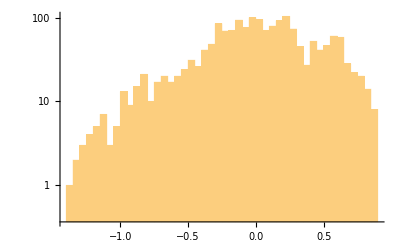

```mathematica
{rawhist,Dynamic[MousePosition["Graphics"]]}
```

```mathematica
SelectionMove[nb,After,CellGroup]
```

Look at structure of the file. Bypass this section.

```mathematica
Manipulate[
ListPlot[Take[xvals,{ilow,ilow+chunk}],Joined->True,Mesh->All,PlotRange->All],{ilow,1,Length[xvals]-chunk-1,250},{{chunk,500},10,Length[xvals]-1,1},SaveDefinitions->True]
```

```mathematica
Manipulate[
ListPlot[Take[yvals,{ilow,ilow+chunk}],Joined->True,Mesh->All,PlotRange->All],{ilow,1,Length[yvals]-chunk-1,1},{{chunk,500},10,Length[yvals]-ilow,1},SaveDefinitions->True]
```

### Trim outlier points.

#### XY Range clean up next. Do each section separately, resetting the main lists each time to the smaller ones.

trim after setting x and y ranges above

```mathematica
{xmin,xmax}={Min[Take[worklist,All,{1}]],Max[Take[worklist,All,{1}]]};
{ymin,ymax}={Min[Take[worklist,All,{2}]],Max[Take[worklist,All,{2}]]};
{zmin,zmax}={Min[Take[worklist,All,{3}]],Max[Take[worklist,All,{3}]]};
```

```mathematica
{{xmin,xmax},{ymin,ymax},{zmin,zmax}}
```

{{1.76812,74.2612},{1.76812,74.2612},{-1.38469,0.880575}}

```mathematica
{{xmin,xmax},{ymin,ymax},{zmin,zmax}}=Input["Enter min,max values here",{{xmin,xmax},{ymin,ymax},{zmin,zmax}}]
```

{{1.76812,74.2612},{1.76812,74.2612},{-1.38469,0.880575}}

```mathematica
SelectionMove[nb,Next,Cell]
```

```mathematica
{xrange,yrange,zrange}={{xmin,xmax},{ymin,ymax},{zmin,zmax}}
```

{{1.76812,74.2612},{1.76812,74.2612},{-1.38469,0.880575}}

```mathematica
xvals=Take[worklist,All,{1}]//Flatten;
yvals=Take[worklist,All,{2}]//Flatten;
zvals=Take[worklist,All,{3}]//Flatten;
```

```mathematica
deltax=xmax-xmin;deltay=ymax-ymin;deltaz=zmax-zmin;{deltax,deltay,deltaz}
```

{72.493,72.493,2.26526}

```mathematica
{xunit$,yunit$,zunit$}
```

{mm,mm,µm}

```mathematica
SelectionMove[nb,Next,Cell]
```

Skip to other clean-up section based on statistics, if desired. Restrict here by x and y range numbers.
NEVER reset worklist. This is the unaltered input data.

```mathematica
Length[worklist]
```

1764

```mathematica
test =
Reap[
 Do[
pt=worklist[[i]];If[pt[[3]]<zrange[[2]]&& pt[[3]]>zrange[[1]]&&pt[[2]]<yrange[[2]]&& pt[[2]]>yrange[[1]]&&pt[[1]]<xrange[[2]]&& pt[[1]]>xrange[[1]]
,Sow[pt]]
,{i,Length[worklist]}]
];
```

```mathematica
Short[test]
```

{Null,{{«1»}}}

```mathematica
trimsurf=Drop[test,1]//Flatten[#,2]&;
```

```mathematica
Length[trimsurf]
```

1599

```mathematica
Remove[test]
```

```mathematica
xvals=Take[trimsurf,All,{1}]//Flatten;
yvals=Take[trimsurf,All,{2}]//Flatten;
zvals=Take[trimsurf,All,{3}]//Flatten;
```

```mathematica
fileinS
```

15433-03-01_Pkg114_-100C_WYKO_cold_flatness

Subtract mean from z. Skip if integer.

```mathematica
meanzflag=False;
```

```mathematica
meanzflag=Input["Set meanzflag to subtract mean from trimsurf data",meanzflag]
```

False

```mathematica
If[meanzflag,meanz=Mean[zvals]//N;trimsurf=Map[MapAt[Plus[#,-meanz]&,#,3]&,trimsurf]]
```

```mathematica
trimsurf[[1;;10]];
```

```mathematica
xvals=Take[trimsurf,All,{1}]//Flatten;
yvals=Take[trimsurf,All,{2}]//Flatten;
zvals=Take[trimsurf,All,{3}]//Flatten;
```

```mathematica
{Mean[xvals],Mean[yvals],Mean[zvals]}//N
```

{38.0019,38.0274,0.0691146}

```mathematica
{xmin=Min[xvals],Mean[xvals],xmax=Max[xvals]}//N
{ymin=Min[yvals],Mean[yvals],ymax=Max[yvals]}//N
{zmin=Min[zvals],Mean[zvals],zmax=Max[zvals]}//N
```

{3.53625,38.0019,72.493}

{3.53625,38.0274,72.493}

{-1.1133,0.0691146,0.880249}

```mathematica
{deltax=xmax-xmin, deltay=ymax-ymin,deltaz=zmax-zmin}
```

{68.9568,68.9568,1.99354}

```mathematica
Length[trimsurf]
```

1599

#### Plot after trimming the X or Y range above. TRIM IT IN PLACE.

```mathematica
skipnum=0
```

0

```mathematica
lpp02=ListPointPlot3D[trimsurf,PlotRange->All,ViewPoint->{0,0,Infinity},ColorFunction->"Rainbow",AxesLabel->{"X "<>xunit$,"Y "<>yunit$,"Z "<>zunit$},PlotLabel->fileinS<>"\nSkip factor = "<>ToString[skipnum]<>", {rows,cols}="<>rowscols$]
```

-Graphics3D-

```mathematica
SelectionMove[nb,Next,Cell]
```

```mathematica
trimsurfplt=ListPointPlot3D[trimsurf,PlotRange->All,ColorFunction->"Rainbow",AxesLabel->{"X "<>xunit$,"Y "<>yunit$,"Z "<>zunit$},PlotLabel->fileinS<>"\nSkip factor = "<>ToString[skipnum]<>", {rows,cols}="<>rowscols$]
```

-Graphics3D-

```mathematica
SelectionMove[nb,Next,Cell]
```

### End of range clean-up iteration section. Contine after subregion is selected.

```mathematica
npts=Length[zvals]
```

1599

```mathematica
SelectionMove[nb,Next,Cell]
```

```mathematica
histplt=Histogram[zvals,50,ImageSize->400];
```

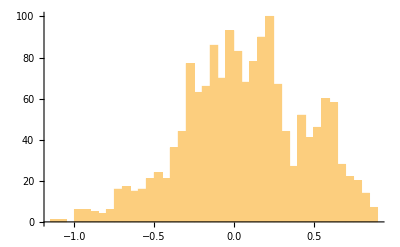

```mathematica
{histplt,Dynamic[MousePosition["Graphics"]]}
```

```mathematica
zsd=StandardDeviation[zvals]//N
```

0.377529

#### Select the appropriate Z trim criteria next. Leave lists empty to use all points without discarding any.

```mathematica
zminlist={};zmaxlist={};
```

```mathematica
{zmin,zmax}
```

{-1.1133,0.880249}

```mathematica
{minq,maxq}=Input["Enter trim range according to histogram above",{zmin,zmax}]
```

{-1.1133,0.880249}

Execute  the following  cell to set the z-trim region . Default is accept all points.

```mathematica
zmaxlist=Select[zvals,#> maxq &];
zminlist=Select[zvals,#< minq &];
```

```mathematica
SelectionMove[nb,Next,Cell]
```

#### Continue here after selecting points to discard, or if no points to discard. Skip if nothing to trim.

```mathematica
{Length[zmaxlist],Length[zminlist]}
```

{0,0}

```mathematica
Union[zmaxlist];
```

```mathematica
Length[%]
```

0

```mathematica
(* Share[] *)
```

```mathematica
outliers=Join[zminlist,zmaxlist];
```

```mathematica
Length[outliers]
```

0

```mathematica
outliers2=Union[outliers];
```

```mathematica
Short[outliers2]
```

{}

```mathematica
plist=Table[Position[zvals,outliers2[[i]]],{i,Length[outliers2]}];
Short[plist]
```

{}

```mathematica
plist=Flatten[plist,1];
```

```mathematica
meanXYZd=.
```

```mathematica
meanXYZt=.
```

```mathematica
trimsurf=Delete[trimsurf,plist];
```

Discard points from the list that lie outside the desired range. Note that the result is a list, not an array. Can't use plot functions that require an array for input.

top is a reduced-size array to use in fitting the surface to avoid excessive calculation time. reduce=1 uses all the points.

```mathematica
Length[worklist]
```

1764

```mathematica
Length[trimsurf]
```

1599

```mathematica
trimsurfplt=ListPlot3D[trimsurf,PlotLabel->fileinS<>"\n{rows,cols}="<>rowscols$,PlotRange->All,BoxRatios->{1,1,.5},AxesLabel->{"X["<>xunit$<>"]","Y["<>yunit$<>"]","Z["<>zunit$<>"]"},ColorFunction->"Rainbow",ImageSize->500]
```

-Graphics3D-

```mathematica
top=.
```

Shorten the data array only if there are too many points. Need to change skipnum value first

```mathematica
skipnum2=.(* *(Length[worklist]//Log[100,#]&//N//Floor) *)
```

```mathematica
zsdev=StandardDeviation[trimsurf][[3]]//N
```

0.377529

```mathematica
rowscols$="sparse";ToString[{nRows,nCols}]
```

{170, 169}

```mathematica
topplt=ListPlot3D[trimsurf,PlotLabel->fileinS<>"\n{rows,cols}="<>rowscols$,PlotRange->All,BoxRatios->{1,1,.5},AxesLabel->{"X["<>xunit$<>"]","Y["<>yunit$<>"]","Z["<>zunit$<>"]"},ColorFunction->"Rainbow",ImageSize->500]
```

-Graphics3D-

Set the worklist to the above trimsurf. Go back up to trim more if desired.

```mathematica
worklist=trimsurf;
```

```mathematica
Length[worklist]
```

1599

```mathematica
SelectionMove[nb,Next,Cell]
```

### Fit edited list to a surface. Enter the surface fit order next. A general set of basis polynomials is calculated and the fit is performed. Enter the x and y orders separately

#### COntinue after fit selection

Select one of the button options, then continue

```mathematica
fitflag=.;fitidxS$=.;fitord$=.
```

```mathematica
fitnumflag=Input["Enter num for fit to apply.\n-1=no detrending\n0 = piston only\n1 = pure plane\n2 = pure sphere\n3 = general {m,n}order polynomial\n4 = Chebyshev polynomial (m,n)" ]
```

-1

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

The working array is worklist. Make sure it has the desired data in it.

Need to normalize the x and y values when doing the Chebyshev fit, using the actual values for xlen and ylen. For the other cases, use xlen=ylen=1 in the normaization expression.

```mathematica
xlen=1;ylen=1;
```

```mathematica
Switch[fitnumflag,
-1,(*No detrend*)fitidxS$="none";Print["No detrend"];fitbasis={0},

0,(*Piston only*)fitbasis={1};fitidxS$="0";Print["Piston only fit"],
1, (*Pure Plane*)fitbasis={1,x,y};fitidxS$="1,1"(*fitord$=StringTake[ToString[fitbasis],{2,-2}]*),
2,(*Pure Sphere*)fitbasis={1,x,y,x y,x^2+y^2};fitidxS$="2,2"(*fitord$=StringTake[ToString[fitbasis//InputForm],{2,-2}]*),

3,(*General cartesian polynomial*)fitidxS$=InputString["Enter x and y order numbers of 2D surface fit desired, separated by a comma, i.e. 1,2"];
sp=StringSplit[fitidxS$,","]//ToExpression;
ordx=sp[[1]];ordy=sp[[2]];
(*fitord$=StringTake[ToString[sp],{2,-2}];*)
fitbasis={};
Do[
If[i+j>ordx+ordy,Null,AppendTo[fitbasis,x^i y^j]],{i,0,ordx},{j,ordy,0,-1}],

4,(*Chebychev poly*)fitidxS$=InputString["Enter x and y order numbers of 2D surface fit desired, separated by a comma, i.e. 1,2"];
sp=StringSplit[fitidxS$,","]//ToExpression;
ordx=sp[[1]];ordy=sp[[2]];
fitidxS$=fitidxS$<>"Chb";
(*fitord$=StringTake[ToString[sp],{2,-2}];*)
(*compute the required xlen and ylen for this case*)
xlen=xmax-xmin//N;ylen=ymax-ymin//N;
fitbasis={};
xs[x_,xmax_,xmin_]:=2/(xmax-xmin) (x-xmin-(xmax-xmin)/2);
fitbasis=Table[HoldForm[ChebyshevT[ii,xs[x,xmax,xmin]]] HoldForm[ChebyshevT[jj,xs[y,ymax,ymin]]]/.ii->i/.jj->j,{i,0,ordx},{j,0,ordy}]//Flatten;

]
```

No detrend

{0}

```mathematica
fitbasis//ReleaseHold//ColumnForm;
```

```mathematica
fitidxS$
```

none

```mathematica
foutname2=fileinS<>"-"<>"S"<>fitidxS$
```

15433-03-01_Pkg114_-100C_WYKO_cold_flatness-Snone

```mathematica
Interrupt[]
```

For Chebyshev, need to release the hold, then Sort the fitbasis to get it in the same order as comes out of the Fit result.
Need to sort the expanded funtions in terms of the highest powers of x and y. Sorting on y lets x-index run fast. This seems to work on both lists.

```mathematica
(*fitbasis2=fitbasis//ReleaseHold;
fitbasissort=fitbasis2//Sort[#,((Exponent[#1,y]<=Exponent[#2,y])&&True)&]&;
fitbasissort//ColumnForm  *)
```

Now calc and sort the fit expression. Need to convert the Head Plus to List by Apply.

```mathematica
surffit=If[fitnumflag==-1,0,Fit[worklist,fitbasis//ReleaseHold,{x,y}]];
```

```mathematica
surffit
```

0

```mathematica
Apply[List,surffit,Heads->True]//ColumnForm;
```

Add separate case here for Chebyshev. Normalize the x and y values before fittiing.

```mathematica
temp=worklist;
```

```mathematica
temp=Map[MapAt[Divide[#,xlen]&,#,1]&,temp];
temp=Map[MapAt[Divide[#,ylen]&,#,2]&,temp];
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
fitsurfplt=Plot3D[surffit,{x,xmin,xmax},{y,ymin,ymax},ColorFunction->"Rainbow",ImageSize->400,PlotLabel->fileinS<>"\nSfit:"<>fitidxS$<>", Rfit:"<>fitidxR$]
```

-Graphics3D-

```mathematica
Button["Export fit surface plot file",Export[foutname2<>"_fitsurf.tiff",fitsurfplt,"ImageEncoding"->"LZW",ImageResolution->100,Method->"Queued"]]
```

Export fit surface plot file

```mathematica
If[testdataflag,testdataflag=False;Interrupt[],Null]
```

If[testdataflag,testdataflag=False;Interrupt[],Null]

When rawXYZ values are in meter units, the radius is in units of meters.

```mathematica
If[c0x!=0.0,Rx=1/(2*c0x),Rx=Infinity]
```

If[c0x≠0.,Rx=1/(2 c0x),Rx=∞]

```mathematica
StringForm["Radius from full 3D surface fit is `` m.",NumberForm[Rx,5]]
```

Radius from full 3D surface fit is Rx m.

```mathematica
resids=.
```

```mathematica
detrworksurf=Table[{worklist[[i,1]],worklist[[i,2]],worklist[[i,3]]-surffit/.x->worklist[[i,1]]/.y->worklist[[i,2]]}
,{i,1,Length[worklist]}
];
```

```mathematica
zresids=.
```

```mathematica
zcloudresids=Take[detrworksurf,All,{3}]//Flatten;
```

```mathematica
maxz=Max[zcloudresids];minz=Min[zcloudresids];meanz=Mean[zcloudresids];medianz=Median[zcloudresids];sigma=StandardDeviation[zcloudresids];
```

```mathematica
skew$=Skewness[zcloudresids]//ToString[#//NumberForm[#,3]&]&
```

-0.182

```mathematica
kurt$=Kurtosis[zcloudresids]//ToString[#//NumberForm[#,3]&]&
```

2.71

```mathematica
sig$=ToString[sigma//NumberForm[#,3]&]
```

0.378

```mathematica
{maxz,minz,sigma}
```

{0.880249,-1.1133,0.377529}

```mathematica
Short[zcloudresids]
```

{-0.660087,-0.611533,«1595»,-0.920137,-1.05559}

```mathematica
zbin=BinCounts[zcloudresids,(maxz-minz)/50]
```

{1,1,0,4,7,3,3,4,5,10,18,8,13,12,19,15,20,18,26,30,52,62,50,49,71,63,56,74,63,55,64,59,78,77,68,36,35,22,47,28,36,39,48,50,29,21,14,15,11,9,1}

```mathematica
quantlist=Reverse[{0.0,0.005,0.01,0.025,0.50,.975,0.99,0.995,1.0}]
```

{1.,0.995,0.99,0.975,0.5,0.025,0.01,0.005,0.}

```mathematica
qres=Quantile[zcloudresids,quantlist]
```

{0.880249,0.840877,0.814882,0.753758,0.0722094,-0.715389,-0.886912,-0.951634,-1.1133}

```mathematica
qtable=Transpose[{quantlist,qres}]
```

{{1.,0.880249},{0.995,0.840877},{0.99,0.814882},{0.975,0.753758},{0.5,0.0722094},{0.025,-0.715389},{0.01,-0.886912},{0.005,-0.951634},{0.,-1.1133}}

```mathematica
qtable//TableForm
```

1. | 0.880249
0.995 | 0.840877
0.99 | 0.814882
0.975 | 0.753758
0.5 | 0.0722094
0.025 | -0.715389
0.01 | -0.886912
0.005 | -0.951634
0. | -1.1133

```mathematica
q100val$=qres[[1]]-qres[[-1]]//NumberForm[#,{6,2}]&//ToString
q100range$={qres[[-1]],qres[[1]]}//NumberForm[#,{6,2}]&//ToString
```

1.99

{-1.11, 0.88}

```mathematica
q99val$=qres[[2]]-qres[[-2]]//NumberForm[#,{6,2}]&//ToString;
q99range$={qres[[-2]],qres[[2]]}//NumberForm[#,{6,2}]&//ToString;
```

```mathematica
q95val$=qres[[4]]-qres[[-4]]//NumberForm[#,{6,2}]&//ToString;
q95range$={qres[[-4]],qres[[4]]}//NumberForm[#,{6,2}]&//ToString;
```

```mathematica
fitidxS$
```

none

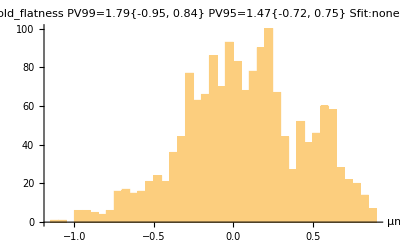

```mathematica
histresidplt=Histogram[zcloudresids,50,ImageSize->400,AxesLabel->{zunit$,""},PlotLabel->fileinS<>"\nPV99="<>q99val$<>q99range$<>" PV95="<>q95val$<>q95range$<>"\nSfit:"<>fitidxS$<>", skew="<>skew$<>", kurt="<>kurt$<>", sdev="<>sig$<>zunit$]
```

```mathematica
Export[foutname2<>"_"<>sig$<>"_histSR.tiff",histresidplt,"ImageEncoding"->"LZW",ImageResolution->100]
```

15433-03-01_Pkg114_-100C_WYKO_cold_flatness-Snone_0.378_histSR.tiff

```mathematica
Button["Export histresid plot file",Export[foutname2<>"_"<>sig$<>"_histSR.tiff",histresidplt,"ImageEncoding"->"LZW",ImageResolution->100]]
```

Export histresid plot file

```mathematica
accumulatedCount[bins_,counts_]:=Accumulate[counts]
```

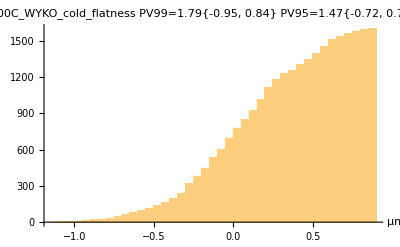

```mathematica
histcumplt=Histogram[zcloudresids,50,accumulatedCount,PlotLabel->fileinS<>"\nPV99="<>q99val$<>q99range$<>" PV95="<>q95val$<>q95range$<>"\nSfit:"<>fitidxS$<>", sdev="<>sig$<>zunit$,AxesLabel->{zunit$,""}]
```

```mathematica
Export[foutname2<>"_"<>sig$<>"_histcumSR.tiff",histcumplt,"ImageEncoding"->"LZW",ImageResolution->100]
```

15433-03-01_Pkg114_-100C_WYKO_cold_flatness-Snone_0.378_histcumSR.tiff

```mathematica
Button["Export histcum plot file",Export[foutname2<>"_"<>sig$<>"_histcumSR.tiff",histcumplt,"ImageEncoding"->"LZW",ImageResolution->100]]
```

Export histcum plot file

```mathematica
filein
```

15433-03-01_Pkg114_-100C_WYKO_cold_flatness.csv

#### Write out the quantile info to xls file and all zresids to text file automatically

```mathematica
Export[foutname2<>"_"<>sig$<>"_zresids.txt",zcloudresids,"Text"]
```

15433-03-01_Pkg114_-100C_WYKO_cold_flatness-Snone_0.378_zresids.txt

```mathematica
Export[foutname2<>"_"<>sig$<>"_Quantiles.xls",Prepend[qtable,{fileinS<>"\nPV99="<>q99val$<>q99range$<>",PV95="<>q95val$<>q95range$<>"\nSfit:"<>fitidxS$<>", sdev="<>sig$<>zunit$}]//TableForm,"XLS"]
```

15433-03-01_Pkg114_-100C_WYKO_cold_flatness-Snone_0.378_Quantiles.xls

```mathematica
quantlist=Reverse[{0.0,0.005,0.01,0.025,0.25,0.50,0.75,0.975,0.99,0.995,1.0}];
```

```mathematica
qresF=Quantile[detrworksurf[[All,-1]]//Flatten,quantlist];
```

```mathematica
Transpose[{quantlist,qresF}]
```

{{1.,0.880249},{0.995,0.840877},{0.99,0.814882},{0.975,0.753758},{0.75,0.325006},{0.5,0.0722094},{0.25,-0.181965},{0.025,-0.715389},{0.01,-0.886912},{0.005,-0.951634},{0.,-1.1133}}

```mathematica
qtableF=Transpose[{quantlist,qresF}];
%//TableForm
```

1. | 0.880249
0.995 | 0.840877
0.99 | 0.814882
0.975 | 0.753758
0.75 | 0.325006
0.5 | 0.0722094
0.25 | -0.181965
0.025 | -0.715389
0.01 | -0.886912
0.005 | -0.951634
0. | -1.1133

```mathematica
qtab1=Join[{{fileinS,"SUT Flatness Quantiles"}},{{"Quantile","Z[µm]"}},qtableF];
```

Output the results file.

```mathematica
detrworksurf//Dimensions
```

{1599,3}

Export statistics

```mathematica
title$="Summary statistics for sensor data file:\n\t `1`\n";
flatline01$="Flatness stats (CCD-031)\n";
flat100$="\tPV100 = `2`µm, range `3`\n";
flat99$="\tPV99 = `4`µm, range `5`\n";
flat95$="\tPV95 = `6`µm, range `7`\t[ ≤10µm spec ]\n";
flatmean$= "Mean = `8`µm\n";
flatmedian$="Median = `9`µm\n";
stdev$="Sigma = `10`µm\n";
qtable$="\nQuantiles\n`11`";
skewlin$="Skewness = `15`\n";
kurtlin$="Kurtosis = `16`\n";
```

```mathematica
qtable//TableForm
```

1. | 0.880249
0.995 | 0.840877
0.99 | 0.814882
0.975 | 0.753758
0.5 | 0.0722094
0.025 | -0.715389
0.01 | -0.886912
0.005 | -0.951634
0. | -1.1133

Date of last mod to this analysis notebook:

```mathematica
nbmod$=DateString["FileModificationTime"/.NotebookInformation[],TimeZone->-10]
```

Fri 27 May 2016 09:36:27

```mathematica
nbname$=CurrentValue["NotebookFileName"]
```

SurfCalc14_e2V_vendor_data_analysis_v04.nb

```mathematica
EvaluationNotebook[]
```

2azi5_shm11FrontEndObject[LinkObject["2azi5_shm", 3, 1]]11SurfCalc14_e2V_vendor_data_analysis_v04.nb/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/_Analysis codes/Vendor Metrology-data-analysis/SurfCalc14_e2V_vendor_data_analysis_v04.nb

```mathematica
filein
```

15433-03-01_Pkg114_-100C_WYKO_cold_flatness.csv

```mathematica
filepathfull
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/_Production DATA/e2V prod sensors/e2V-114/15433-03-01_Pkg114_-100C_WYKO_cold_flatness.csv

```mathematica
FileDate[CurrentValue["NotebookFullFileName"],"Modification"]
```

Fri 27 May 2016 11:36:27GMT-4.

```mathematica
LocalTime[]
```

Fri 27 May 2016 12:16:45GMT-4.

```mathematica
statreport=StringTemplate[StringJoin[title$,flatline01$,flat100$,flat99$,flat95$,flatmean$,flatmedian$,stdev$,skewlin$,kurtlin$,qtable$,"\n\nReport generated `12`\nNotebook version: `13`\nLast modified: `14`"]][filein,q100val$,q100range$,q99val$,q99range$,q95val$,q95range$,meanz//NumberForm[#,{6,2}]&//ToString,medianz//NumberForm[#,{6,2}]&//ToString,sig$,qtable//TableForm,DateString[],nbname$,nbmod$,skew$,kurt$]
```

Summary statistics for sensor data file:
	 15433-03-01_Pkg114_-100C_WYKO_cold_flatness.csv
Flatness stats (CCD-031)
	PV100 = 1.99µm, range {-1.11, 0.88}
	PV99 = 1.79µm, range {-0.95, 0.84}
	PV95 = 1.47µm, range {-0.72, 0.75}	[ ≤10µm spec ]
Mean = 0.07µm
Median = 0.07µm
Sigma = 0.378µm
Skewness = -0.182
Kurtosis = 2.71

Quantiles
1.    0.880249
0.995 0.840878
0.99  0.814882
0.975 0.753758
0.5   0.0722094
0.025 -0.715389
0.01  -0.886912
0.005 -0.951634
0.    -1.1133

Report generated Fri 27 May 2016 12:16:45
Notebook version: SurfCalc14_e2V_vendor_data_analysis_v04.nb
Last modified: Fri 27 May 2016 09:36:27

```mathematica
Export[foutname2<>"_"<>sig$<>"_e2V_stat_report.txt",statreport,"TEXT"]
```

15433-03-01_Pkg114_-100C_WYKO_cold_flatness-Snone_0.378_e2V_stat_report.txt

```mathematica
Button["Export Flatness statistics TXT file.",Export[foutname2<>"_e2V_stat_report.txt",statreport,"TEXT"]]
```

Export Flatness statistics TXT file.

```mathematica
binwid=(maxz-minz)/25;
```

```mathematica
bcts=BinCounts[zcloudresids,binwid]
```

{2,4,10,7,15,26,25,34,38,56,114,99,134,130,118,123,155,104,57,75,75,98,50,29,20,1}

```mathematica
Mean[zcloudresids]
```

0.0691146

```mathematica
sd=sigma//N
```

0.377529

```mathematica
zwid=4 sd
```

1.51011

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

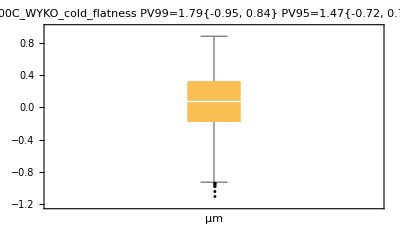

```mathematica
bwc=BoxWhiskerChart[zcloudresids,"Outliers",ImageSize->400,PlotLabel->fileinS<>"\nPV99="<>q99val$<>q99range$<>" PV95="<>q95val$<>q95range$<>"\nSfit:"<>fitidxS$<>", sdev="<>sig$<>zunit$,AxesLabel->{zunit$,""}]
```

```mathematica
Export[foutname2<>"_"<>sig$<>"_boxwhisker.tiff",bwc,"ImageEncoding"->"LZW",ImageResolution->100]
```

15433-03-01_Pkg114_-100C_WYKO_cold_flatness-Snone_0.378_boxwhisker.tiff

```mathematica
Button["Export box whisker chart file",Export[foutname2<>"_"<>sig$<>"_boxwhisker.tiff",bwc,"ImageEncoding"->"LZW",ImageResolution->100]]
```

Export box whisker chart file

#### Plot detrended trim array. Eliminate the dropouts with the RegionFunction.

```mathematica
{minz,maxz}={Min[zcloudresids],Max[zcloudresids]}
```

{-1.1133,0.880249}

```mathematica
PV=maxz-minz
```

1.99354

```mathematica
q100val$
```

1.99

```mathematica
zrange={minz,maxz}
```

{-1.1133,0.880249}

```mathematica
q100range$
```

{-1.11, 0.88}

Plot detrended point cloud next:

```mathematica
vp=.
```

```mathematica
vp=Options[ListPointPlot3D,ViewPoint][[1,2]]
```

{1.3,-2.4,2.}

```mathematica
Dynamic[vp]
```

```mathematica
lpplt=ListPointPlot3D[detrworksurf,PlotRange->All,ColorFunction->"Rainbow",(*BoxRatios->{Automatic,Automatic,Automatic},*)AxesLabel->{"Xval","Yval","Z["<>zunit$<>"]"},PlotLabel->fileinS<>"\nPV99="<>q99val$<>q99range$<>" PV95="<>q95val$<>q95range$<>"\nSfit:"<>fitidxS$<>", sdev="<>sig$<>zunit$,ImageSize->400,ViewPoint->Dynamic[vp],PlotLegends->Automatic];
```

Output the detrended data triplets

```mathematica
Export[foutname2<>"_"<>sig$<>"_DetrendXYZ.txt",detrworksurf,"Text"]
```

15433-03-01_Pkg114_-100C_WYKO_cold_flatness-Snone_0.378_DetrendXYZ.txt

```mathematica
Button["Export detrworksurf data text file",Export[foutname2<>"_"<>sig$<>"_DetrendXYZ.txt",detrworksurf,"Text"]]
```

Export detrworksurf data text file

```mathematica
lpplt2=Show[lpplt,ViewPoint->Dynamic[vp]]
```

-Graphics3D-

```mathematica
Export[foutname2<>"_"<>sig$<>"_3Dpts.tiff",lpplt2,"ImageEncoding"->"LZW",ImageResolution->100,Method->"Queued"]
```

15433-03-01_Pkg114_-100C_WYKO_cold_flatness-Snone_0.378_3Dpts.tiff

```mathematica
Button["Export lpplt2 plot file",Export[foutname2<>"_"<>sig$<>"_3Dpts.tiff",lpplt2,"ImageEncoding"->"LZW",ImageResolution->100,Method->"Queued"]]
```

Export lpplt2 plot file

```mathematica
Directory[]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/_Production DATA/e2V prod sensors/e2V-114/15433-03-01_Pkg114_-100C_WYKO_cold_flatness_files

Define a tick function to scale the values by some scaleval factor

```mathematica
ticksw[wmin_,wmax_,scaleval_,interval_]:=Table[{i,Floor[i  scaleval]},{i,wmin,wmax,interval}]
```

```mathematica
lpdetr=ListPlot3D[detrworksurf,InterpolationOrder->1,MaxPlotPoints->Min[50,Sqrt[Length[detrworksurf]]//IntegerPart],ImageSize->400,PlotRange->All,BoxRatios->{deltax/deltay,1,1/2},Mesh->None,ColorFunction->"Rainbow",ColorFunctionScaling->True,AxesLabel->{"Xcol["<>xunit$<>"]","Yrow["<>yunit$<>"]","Z["<>zunit$<>"]"},PlotLabel->fileinS<>"\nPV99="<>q99val$<>q99range$<>" PV95="<>q95val$<>q95range$<>"\nSfit:"<>fitidxS$<>", sdev="<>sig$<>zunit$,Ticks->{ticksw[xmin,xmax,1,Ceiling[(xmax-xmin)/6,10]],ticksw[ymin,ymax,1,Ceiling[(ymax-ymin)/6,10]],Automatic},PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
Export[foutname2<>"_"<>sig$<>"_3Dsurf.tiff",lpdetr,"ImageEncoding"->"LZW",ImageResolution->100,Method->"Queued"]
```

15433-03-01_Pkg114_-100C_WYKO_cold_flatness-Snone_0.378_3Dsurf.tiff

```mathematica
Button["Export lpdetr plot file",Export[foutname2<>"_"<>sig$<>"_3Dsurf.tiff",lpdetr,"ImageEncoding"->"LZW",ImageResolution->100,Method->"Queued"]]
```

Export lpdetr plot file

Compute list resids. These are xyz triplets.

```mathematica
(*Share[]*)
```

```mathematica
zsd=StandardDeviation[detrworksurf][[3]]
```

0.377529

```mathematica
zsd==sigma
```

True

```mathematica
lpresid=.;lpresid2=.;
```

```mathematica
plotallflag=True;
```

```mathematica
If[plotallflag,lpresid=ListPlot3D[detrworksurf,PlotRange->{All,All,All},ColorFunction->"Rainbow",MaxPlotPoints->Min[50,Sqrt[Length[detrworksurf]]//IntegerPart],BoxRatios->{deltax/deltay,1,1/2},ColorFunctionScaling->True,AxesLabel->{"Xcol["<>xunit$<>"]","Yrow["<>yunit$<>"]","Z["<>zunit$<>"]"},PlotLabel->fileinS<>"\nPV99="<>q99val$<>q99range$<>" PV95="<>q95val$<>q95range$<>"\nSfit:"<>fitidxS$<>", sdev="<>sig$<>zunit$,ImageSize->400,Ticks->{ticksw[xmin,xmax,1,Ceiling[(xmax-xmin)/6,10]],ticksw[ymin,ymax,1,Ceiling[(ymax-ymin)/6,10]],Automatic},PlotLegends->Automatic]; 
lpresid2=lpresid
]
```

-Graphics3D-

```mathematica
foutname2<>ToString[sig$]
```

15433-03-01_Pkg114_-100C_WYKO_cold_flatness-Snone0.378

```mathematica
Export[foutname2<>"_"<>sig$<>"_3Dsurfgrid.tiff",lpresid2,"ImageEncoding"->"LZW",ImageResolution->100,Method->"Queued"]
```

15433-03-01_Pkg114_-100C_WYKO_cold_flatness-Snone_0.378_3Dsurfgrid.tiff

```mathematica
Button["Export lpresid2 plot file",Export[foutname2<>"_"<>sig$<>"_3Dsurfgrid.tiff",lpresid2,"ImageEncoding"->"LZW",ImageResolution->100,Method->"Queued"]]
```

Export lpresid2 plot file

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
ColorData["Named"]
```

{Atoms,Crayola,GeologicAges,HTML,Legacy,WebSafe}

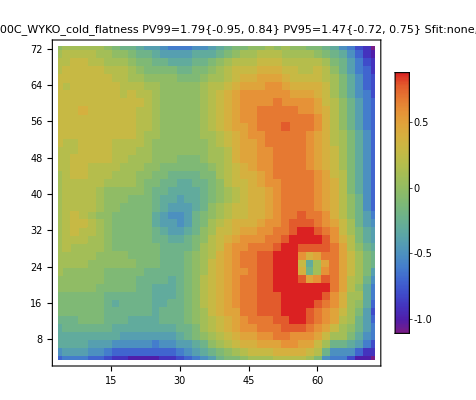

```mathematica
cplt=ListContourPlot[detrworksurf,PlotRange->All,MaxPlotPoints->Min[50,Sqrt[Length[detrworksurf]]//IntegerPart],ColorFunction->"Rainbow",Contours->20,PlotLabel->fileinS<>"\nPV99="<>q99val$<>q99range$<>" PV95="<>q95val$<>q95range$<>"\nSfit:"<>fitidxS$<>", sdev="<>sig$<>zunit$,PlotLegends->Automatic,InterpolationOrder->0]
```

```mathematica
Export[foutname2<>"_"<>sig$<>"_contour.tiff",cplt,"ImageEncoding"->"LZW",ImageResolution->100,Method->"Queued"]
```

15433-03-01_Pkg114_-100C_WYKO_cold_flatness-Snone_0.378_contour.tiff

```mathematica
Button["Export contour plot file",Export[foutname2<>"_"<>sig$<>"_contour.tiff",cplt,"ImageEncoding"->"LZW",ImageResolution->100,Method->"Queued"]]
```

Export contour plot file

Iterate selection next:

```mathematica
Input["Select one of the worklist assignments.\nOr just go back up to new fit to use previous data."]
```

STOP HERE

```mathematica
worklist=detrworksurf; (* if you like the current detrened surface *)
```

```mathematica
worklist=trimsurf; (* if you want to restart with the original trimmed data *)
```

To iterate, execute one of the next locates.

```mathematica
NotebookLocate["new fit" ] (* go back up to change the fit order with the original data *)
```

```mathematica
NotebookLocate["Remove bad points"] (* to remove more bad points from worklist *)
```

```mathematica
NotebookLocate["Restart from urdataSR"] (* to restore all the trimmed points and restart the analysis *)
```

Define array names:
  ursurf == Initial input data readin
  trimsurf == trimmed of bad points
  worklist == working array starting point for detrending
  detrworksurf == work surf after detrending

For next input file:

```mathematica
NotebookLocate["pick MST file num"]
```

### Countor plots next

resids are triplets

```mathematica
Dimensions[detrworksurf]
```

{1599,3}

```mathematica
cloudXYZtrdet=detrworksurf;
```

```mathematica
Dimensions[cloudXYZtrdet]
```

{1599,3}

```mathematica
cloudXYZtrdet[[1;;10]]
```

{{3.53625,3.53625,-0.660087},{5.30437,3.53625,-0.611533},{7.07249,3.53625,-0.601897},{8.84061,3.53625,-0.632459},{10.6087,3.53625,-0.687139},{12.3769,3.53625,-0.742419},{14.145,3.53625,-0.810591},{15.9131,3.53625,-0.874916},{17.6812,3.53625,-0.928096},{19.4493,3.53625,-0.956496}}

```mathematica
Zstddev=StandardDeviation[cloudXYZtrdet][[3]]
```

0.377529

```mathematica
{minX,maxX}={Min[Take[cloudXYZtrdet,All,{1}]],Max[Take[cloudXYZtrdet,All,{1}]]};
{minY,maxY}={Min[Take[cloudXYZtrdet,All,{2}]],Max[Take[cloudXYZtrdet,All,{2}]]};
{minz1,maxz1}={Min[Take[cloudXYZtrdet,All,{3}]],Max[Take[cloudXYZtrdet,All,{3}]]}
```

{-1.1133,0.880249}

```mathematica
(*{minz1,maxz1}={-6,6}*Zstddev *)
```

```mathematica
PlotLabel->fileinS<>"\nPV99="<>q99val$<>q99range$<>" PV95="<>q95val$<>q95range$<>"\nSfit:"<>fitidxS$<>", sdev="<>sig$<>zunit$
```

PlotLabel→15433-03-01_Pkg114_-100C_WYKO_cold_flatness
PV99=1.79{-0.95, 0.84} PV95=1.47{-0.72, 0.75}
Sfit:none, sdev=0.378µm

```mathematica
fileinS
```

15433-03-01_Pkg114_-100C_WYKO_cold_flatness

```mathematica
PlotRange->{{0,(maxz1-minz1)/21},{minz1,maxz1}}
```

PlotRange→{{0,0.0949307},{-1.1133,0.880249}}

```mathematica
AxesLabel->{"X["<>xunit$<>"]","Y["<>yunit$<>"]"}
```

AxesLabel→{X[mm],Y[mm]}

```mathematica
{minz1,maxz1}
```

{-1.1133,0.880249}

```mathematica
PV=maxz1-minz1
```

1.99354

```mathematica
aspct=(xrange[[2]]-xrange[[1]])/(yrange[[2]]-yrange[[1]])
```

1.

```mathematica
FrameTicks->{ticksw[xmin,xmax,delx,150],ticksw[ymin,ymax,dely,150]}
```

FrameTicks→{{{3.53625,6}},{{3.53625,6}}}

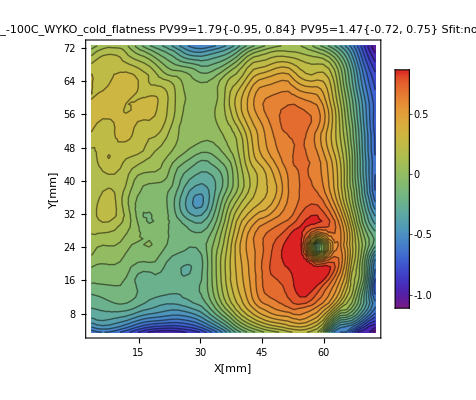

```mathematica
cplt=ListContourPlot[cloudXYZtrdet,PlotRange->All,Contours->25,MaxPlotPoints->Min[50,Length[cloudXYZtrdet]],InterpolationOrder->1,Axes->False,FrameLabel->{"X["<>xunit$<>"]","Y["<>yunit$<>"]"},ColorFunction->"Rainbow",Mesh->False,ImageSize->400 ,AspectRatio->Automatic,PlotLabel->fileinS<>"\nPV99="<>q99val$<>q99range$<>" PV95="<>q95val$<>q95range$<>"\nSfit:"<>fitidxS$<>", sdev="<>sig$<>zunit$,PlotLegends->Automatic]
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
Button["Export cplt contour plot file",Export[foutname2<>"_"<>sig$<>"_contour2.tiff",cplt,"ImageEncoding"->"LZW",ImageResolution->100]]
```

Export cplt contour plot file

```mathematica
Button["Export cplt contour plot PNG file",Export[foutname2<>"_"<>sig$<>"_contour2.png",cplt,"ImageEncoding"->"LZW",ImageResolution->100,Method->"Queued"]]
```

Export cplt contour plot PNG file

```mathematica
Dimensions[cloudXYZtrdet]
```

```mathematica
Short[cloudXYZtrdet,5]
```

```mathematica
NotebookLocate["iteration start"]
```

```mathematica
NotebookLocate["pick MST file num"]
```

## View sections of the original big surface in datain3. Compute surface gradient plot on selected area. (Not for FREEFORM data)

```mathematica
Dimensions[sparseXYZtrdet]
```

```mathematica
(*datain3=resids; *)
```

```mathematica
datain3[[1]]
```

```mathematica
nrows
```

```mathematica
ncols
```

```mathematica
ncols nrows
```

```mathematica
Length[datain3]
```

```mathematica
Length[datain3]/ncols
```

```mathematica
datain32D=.
```

Partition the original datain3 triplets into a 2D array.

```mathematica
datain3[[1]]
```

```mathematica
datain32D=Partition[datain3,ncols];
```

```mathematica
Length[datain32D]
```

```mathematica
fitidxS$=InputString["Enter x and y order numbers of 2D surface fit desired, separated by a comma, i.e. 1,2"];
sp=StringSplit[fitidxS$,","]//ToExpression;
ordx=sp[[1]];ordy=sp[[2]];
fitbasis={};
Do[
If[i+j>ordx+ordy,Null,AppendTo[fitbasis,x^i y^j]],{i,0,ordx},{j,0,ordy-i}];fitbasis
```

```mathematica
Dimensions[datain32D]
```

```mathematica
rstart=1;rinc=10;colleft=1;colinc=20;
```

```mathematica
Manipulate[
subdatlist=Take[datain32D,{rstart,rstart+rinc},{colleft,colleft+colinc}]//Flatten[#,1]&;
surffit[x_,y_]=Fit[subdatlist,fitbasis,{x,y}];

resids=Table[{subdatlist[[i,1]],subdatlist[[i,2]],subdatlist[[i,3]]-surffit[subdatlist[[i,1]],subdatlist[[i,2]]]}
,{i,1,Length[subdatlist]}
];
residsZ=Take[resids,All,{3}]//Flatten;
sdz=StandardDeviation[residsZ];
residsZarr=Partition[residsZ,colinc+1];
range$=ToString[{{rstart,rstart+rinc},{colleft,colleft+colinc}}];
ListPlot3D[residsZarr,ColorFunction->Automatic,Mesh->False,PlotRange->All,MaxPlotPoints->200,BoxRatios->{(colinc/rinc),1,1/2},PlotLabel->filein<>"\nStdDev="<>ToString[sdz]<>", Pixel size="<>ToString[pixSize]<>", Range="<>range$,DataRange->{delx{colleft,colleft+colinc},dely{rstart,rstart+rinc}},AxesLabel->{"Col X[µm]","Row Y[µm]","Z[µm]"}],

{{rstart,1,"Start row"},1,nrows-rinc-1,1,Appearance->"Open"},{{rinc,20,"Row range"},1,nrows-rstart-1,1,Appearance->"Open"},{{colleft,1,"LeftColmn"},1,ncols-colinc-1,1,Appearance->"Open"},{{colinc,Ceiling[(ncols-colleft)/10],"DeltaColmns"},1,ncols-colleft,1,Appearance->"Open"},
TrackedSymbols:>True,ContinuousAction->False,SynchronousUpdating->False,AppearanceElements->All,LocalizeVariables->False,SaveDefinitions->True]
```

```mathematica
datain32D//Short[#,10]&
```

```mathematica
Histogram[residsZ,AxesLabel->{zunit$,""},PlotLabel->filein<>"\nStdDev="<>ToString[sdz]<>", RCrange="<>range$]
```

```mathematica
residsZarr[[10,10]]
```

```mathematica
mediansd1=MedianDeviation[residsZ]
```

What is corrct normalization for slope kernal? 2pt differences should just divide by delx.

```mathematica
lanN=4;
```

```mathematica
lanczoslist=Table[3 k /(lanN (lanN+1) (2 lanN +1)),{k,-lanN,lanN}]
```

```mathematica
lancospos= Table[{lanN+1,i},{i,1,2 lanN +1}]
```

```mathematica
lkernal=SparseArray[lancospos->lanczoslist,2 lanN +1]
```

```mathematica
lanczosmatrixX[lanN_]:=Module[{},lanczoslist=Table[3 k /(lanN (lanN+1) (2 lanN +1)),{k,-lanN,lanN}];lancospos= Table[{lanN+1,i},{i,1,2 lanN +1}];
lkernal=SparseArray[lancospos->lanczoslist,2 lanN +1];
lk=lkernal//Normal
]
```

```mathematica
lanczosmatrixY[lanN_]:=Module[{},lanczoslist=Table[3 k /(lanN (lanN+1) (2 lanN +1)),{k,-lanN,lanN}];lancospos= Table[{lanN+1,i},{i,1,2 lanN +1}];
lkernal=SparseArray[lancospos->lanczoslist,2 lanN +1];
lk=Transpose[lkernal]//Normal
]
```

```mathematica
lanczosmatrixY[lanN]
```

```mathematica
lanczosmatrix[lanN_]:=Module[{},lanczoslist=Table[3 k /(lanN (lanN+1) (2 lanN +1)),{k,-lanN,lanN}];lancospos= Table[{lanN+1,i},{i,1,2 lanN +1}];
lkernal=SparseArray[lancospos->lanczoslist,2 lanN +1];
lk=lkernal+Transpose[lkernal]//Normal
]
```

```mathematica
delx
```

```mathematica
toMicroRad=10^6;
```

```mathematica
slopex=ListConvolve[lanczosmatrixX[lanN],residsZarr]toMicroRad/delx;
```

```mathematica
slopey=ListConvolve[lanczosmatrixY[lanN],residsZarr]toMicroRad/delx;
```

```mathematica
slopexy=ListConvolve[lanczosmatrix[lanN],residsZarr]toMicroRad/delx;
```

```mathematica
meanslp=Mean[StandardDeviation[slopexy]]*toMicroRad (* in microrads *)
```

```mathematica
medianslp=Median[StandardDeviation[slopexy]]*toMicroRad (* in microrads *)
```

```mathematica
gradient=Sqrt[slopex^2 +slopey^2];
```

```mathematica
medGrad=Median[StandardDeviation[gradient]]
```

```mathematica
Max[gradient]
```

```mathematica
Min[gradient]
```

```mathematica
sd2D
```

```mathematica
StandardDeviation[Flatten[gradient]]
```

```mathematica
meansdg=Mean[StandardDeviation[gradient]] (* in microrads *)
```

```mathematica
StandardDeviation[Flatten[gradient]]
```

```mathematica
(*gradient2=ListConvolve[{{1,1,1}/3,{1,1,1}/3},gradient];*)
```

```mathematica
gradientplt=ListPlot3D[gradient,ColorFunction->Automatic,Mesh->False,ImageSize->400,PlotRange->{0,10 medGrad},MaxPlotPoints->200,BoxRatios->{(colinc/rinc),1,1/2},DataRange->{delx{colleft,colleft+colinc},dely{rstart,rstart+rinc}},PlotLabel->filein<>"\n2D Gradient Mag StdDev="<>ToString[Mean[StandardDeviation[gradient]]]<>" µrad, Range="<>range$,AxesLabel->{"Col X[µm]","Row Y[µm]","Slope[µrad]"}]
```

```mathematica
ListContourPlot[gradient]
```

```mathematica
ListPlot3D[slopexy ,ColorFunction->Automatic,Mesh->False,PlotRange->All,ImageSize->400,MaxPlotPoints->200,BoxRatios->{(colinc/rinc),1,1/2},DataRange->{delx{colleft,colleft+colinc},dely{rstart,rstart+rinc}},PlotLabel->filein<>"\nSlope StdDev="<>ToString[Mean[StandardDeviation[slopexy]] ]<>" µrad, Range="<>range$,AxesLabel->{"Col X[µm]","Row Y[µm]","Slope[µrad]"}]
```

```mathematica
(* Share[] *)
```

```mathematica
Mean[StandardDeviation[slopexy]] (* in microrads *)
```

```mathematica
Dimensions[slopex]
```

```mathematica
Show[bumpslopeplt]
```

```mathematica
ListPlot3D[slopex ,ColorFunction->Automatic,Mesh->False,PlotRange->All,ImageSize->400,MaxPlotPoints->200,BoxRatios->{(colinc/rinc),1,1/2},DataRange->{delx{colleft,colleft+colinc},dely{rstart,rstart+rinc}},PlotLabel->filein<>"\nSlope StdDev="<>ToString[Mean[StandardDeviation[slopex]]]<>" µrad, Range="<>range$,AxesLabel->{"Col X[µm]","Row Y[µm]","Slope[µrad]"}]
```

```mathematica
ListPlot3D[slopey ,ColorFunction->Automatic,Mesh->False,PlotRange->All,ImageSize->400,MaxPlotPoints->200,BoxRatios->{(colinc/rinc),1,1/2},DataRange->{delx{colleft,colleft+colinc},dely{rstart,rstart+rinc}},PlotLabel->filein<>"\nSlope StdDev="<>ToString[Mean[StandardDeviation[slopey]]]<>" µrad, Range="<>range$,AxesLabel->{"Col X[µm]","Row Y[µm]","Slope[µrad]"}]
```

```mathematica
ListPlot3D[(slopex+slopey) ,ColorFunction->Automatic,Mesh->False,PlotRange->Automatic,MaxPlotPoints->200,BoxRatios->{(colinc/rinc),1,1/2},DataRange->{delx{colleft,colleft+colinc},dely{rstart,rstart+rinc}},ImageSize->400,PlotLabel->filein<>"\nSlope StdDev="<>ToString[Mean[StandardDeviation[slopex+slopey]]*10^6 ]<>" µrad, Range="<>range$,AxesLabel->{"Col X[µm]","Row Y[µm]","Slope[µrad]"}]
```

## Junk

#### Yvals: Remove points from list with yvals outside of desired range.

```mathematica
yrange={40,80};(*Clean up outliers from tile*)
```

```mathematica
yrange={64,66};
```

```mathematica
ymaxlist=Select[yvals,#>yrange[[2]] &];yminlist=Select[yvals,#<yrange[[1]] &];
```

```mathematica
Length[ymaxlist]
```

```mathematica
outliers=Join[yminlist,ymaxlist];
```

```mathematica
Length[outliers]
```

```mathematica
outliers2=Union[outliers];
```

```mathematica
ProgressIndicator[Dynamic[nn],{1,Length[outliers2]}]
```

```mathematica
plist=Table[(nn=i;Position[yvals,outliers2[[i]]]),{i,Length[outliers2]}];
Short[plist]
```

```mathematica
plist=Flatten[plist,1];
```

```mathematica
Interrupt[]
```

```mathematica
test=Reap[Map[If[#[[2]]>yrange[[2]]∨ #[[2]]<yrange[[1]],Sow[#]]&,sparseXYZ],_?Real];
```

```mathematica
yrange[[1]]
```

```mathematica
test=.
```

```mathematica
test =Reap[ Do[If[sparseXYZ[[i]][[2]]<yrange[[2]]&& sparseXYZ[[i]][[2]]>yrange[[1]],Sow[sparseXYZ[[i]]]],{i,Length[sparseXYZ]}]];
```

```mathematica
Length[test]
```

```mathematica
sparseXYZ[[1]]
```

```mathematica
Short[test,5]
```

```mathematica
Map[MapAt[Times[#,10^3]&,#,3]&,urdataS]
```

#### Xvals: Remove points from list with xvals outside of desired range.

```mathematica
xrange={81,84};(*Clean up outliers from tile*)
```

```mathematica
xmaxlist=Select[xvals,#>xrange[[2]] &];xminlist=Select[xvals,#<xrange[[1]] &];
```

```mathematica
Length[xmaxlist]
```

```mathematica
outliers=Join[xminlist,xmaxlist];
```

```mathematica
Length[outliers]
```

```mathematica
outliers2=Union[outliers];
```

```mathematica
plist=Table[Position[xvals,outliers2[[i]]],{i,Length[outliers2]}];
Short[plist]
```

```mathematica
plist=Flatten[plist,1];
```

```mathematica
xv=Take[xvals,4000];
yv=Take[yvals,4000];
zv=Take[zvals,4000];
```

```mathematica
temp=Take[sparseXYZ,{10000,10010}]
```

```mathematica
ListPlot[xv]
```

```mathematica
xv[[1;;10]]
```

```mathematica
xv=xv-xv[[1]];
```

```mathematica
xv=1000 xv;
```

```mathematica
test=Map[IntegerPart[#]&,xv];
```

```mathematica
temp
```

```mathematica
IntegerPart[1000 Map[(#-sparseXYZ[[1]])&,temp,1]]
```

Reset xvals, yvals, zvals to the new range

```mathematica
xvals=Take[sparseXYZ,All,{1}]//Flatten;
yvals=Take[sparseXYZ,All,{2}]//Flatten;
zvals=Take[sparseXYZ,All,{3}]//Flatten;
```

```mathematica
meanz=Mean[zvals]
```

```mathematica
sparseXYZ=Map[MapAt[Plus[#,-meanz]&,#,3]&,sparseXYZ];
```

```mathematica
zvals=zvals-Mean[zvals];
```

```mathematica
Mean[zvals]
```

Extract the z-values from the list. Find the position of the bad points. Replace the numbers with I. THen partition by cols.
ListDensityPlot then ignores points that are not a real number.

```mathematica
sparsezvals=Take[sparseXYZ,All,{3}]//Flatten;
```

```mathematica
ListPlot[sparsezvals]
```

Convert to integers if desired: Skip if not desired.

```mathematica
sparseXYZint=.
```

```mathematica
intflag=False;
```

```mathematica
If[intflag==True,sparseXYZint=Map[1000 IntegerPart[#]&,sparseXYZ,1];sparseXYZint[[1;;10]]]
```

MST sparse data: turm x&y indexes to mm; leave z in µm.

```mathematica
delx
```

```mathematica
sparseXYZ=Map[MapAt[Times[#,1.0]&,#,3]&,sparseXYZ];
```

```mathematica
sparseXYZ=Map[MapAt[Times[#,delx/1000]&,#,1]&,sparseXYZ];
```

```mathematica
sparseXYZ=Map[MapAt[Times[#,delx/1000]&,#,2]&,sparseXYZ];
```

```mathematica
sparseXYZ[[2]]
```

File input functions

```mathematica
If[$OperatingSystem=="MacOSX",filenamefull=StringDrop[filepathfull,{1,Last[StringPosition[filepathfull,"/"]][[1]]}]
,filenamefull=StringDrop[filepathfull,{1,Last[StringPosition[filepathfull,"\\"]][[1]]}]]
```

```mathematica
filenamefull=StringDrop[filepath,{1,Last[StringPosition[filepathfull,sep$]][[1]]}]
```

```mathematica
streamfile=OpenRead[filepathfull]
```

```mathematica
SetStreamPosition[streamfile,0]
```

```mathematica
Transpose[Take[Transpose[Position[datain,"EOR",2]],{1}]]
```

```mathematica
contourPos2=Union[Transpose[Take[Transpose[Position[datain,"Contour",2]],{1}]],Position[datain,{},2],Transpose[Take[Transpose[Position[datain,"EOR",2]],{1}]]]
```

```mathematica
Length[datain]
```

```mathematica
datain2=Delete[datain,contourPos2];
```

```mathematica
Length[datain2]
```

```mathematica
datain2=Delete[datain2,1];(*This strips off 1st element header record*)
```

```mathematica
datain[[490;;515]]
```

```mathematica
Button["General polynomial fit",fitflag=True;Print["Set fitbasis next."]]

Button["Pure Plane fit",fitbasis={1,x,y};fitidxS$="1,1";fitflag=False;fitord$=StringTake[ToString[fitbasis],{2,-2}];Print["fitbasis =",fitbasis]]

Button["Pure Sphere surface",fitflag=False;fitbasis={1,x,y,x y,x^2+y^2};fitidxS$="2,2";fitord$=StringTake[ToString[fitbasis//InputForm],{2,-2}];Print["fitbasis =",fitbasis]]
```

```mathematica
If[fitflag
,fitidxS$=InputString["Enter x and y order numbers of 2D surface fit desired, separated by a comma, i.e. 1,2"];
fitidxS$;
sp=StringSplit[fitidxS$,","]//ToExpression;
ordx=sp[[1]];ordy=sp[[2]];Print["ordx ",ordx," ordy ",ordy];
fitord$=StringTake[ToString[sp],{2,-2}];
fitbasis={};
Do[
If[i+j>ordx+ordy,Null,AppendTo[fitbasis,x^i y^j];Print[{i,j,fitbasis}]],{i,0,ordx},{j,ordy,0,-1}]
,
fitidxS$=fitidxS$];
fitbasis
```

## Compare surface fit eqns

```mathematica
eqn1=Get["/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/Raft2 130627/CalFlat130627_1x1mm_Xdir_3,5_REFsurfFiteqn"]
```

```mathematica
eqn2=Get["/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/Raft2 130627/CalFlat130627_1x1mm_Xdir2_3,5_REFsurfFiteqn"]
```

```mathematica
Plot3D[{eqn1,eqn2},{x,0,120},{y,0,126},AxesLabel->{"X","Y","Z"}]
```

```mathematica
xdifs=Plot3D[{eqn1-eqn2},{x,0,120},{y,0,126},PlotRange->All,AxesLabel->{"X","Y","Z"},PlotStyle->{Opacity[0.5],Red}]
```

```mathematica
eqn3=Get["/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/Raft2 130627/CalFlat130627_2x2mm_ydir_3,5_REFsurfFiteqn"]
```

```mathematica
eqn4=Get["/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/Flatness_raft/Raft2 130627/CalFlat130627_2x2mm_ydir2_3,5_REFsurfFiteqn"]
```

```mathematica
Plot3D[{eqn1,eqn2,eqn3,eqn4},{x,0,120},{y,0,126},AxesLabel->{"X","Y","Z"},PlotStyle->{Opacity[0.5],Red,Red,Blue,Blue}]
```

```mathematica
ydifs=Plot3D[{eqn4-eqn3},{x,0,120},{y,0,126},PlotRange->All,AxesLabel->{"X","Y","Z"},PlotStyle->{Opacity[0.5],Blue}]
```

```mathematica
Show[xdifs,ydifs]
```

#### Return here after the test surface has been run through the fitting routine.

View the fit parameters returned by the fitting routine. Arrage them in the same order as for the input surface coefficients.

```mathematica
flist=MonomialList[surffit[x,y],"NegativeDegreeReverseLexicographic"]//Sort[#]&;
%//TableForm
```

```mathematica
slist=MonomialList[compsurfeqn]//Sort[#]&;
%//TableForm
```

View both the input and output coefficients:

```mathematica
slist//ColumnForm
```

```mathematica
{slist,flist}
```

```mathematica
{Prepend[slist,0.]//ColumnForm,flist//ColumnForm}
```

```mathematica
Show[fitsurfplt,insurfplt]
```

### Unknown text file parameters

```mathematica
SetStreamPosition[streamfile,0]
```

Skip header read is only data triplets.

```mathematica
header=ReadList[streamfile,Record,5]//TableForm
```

Continue after header read to read in data.

```mathematica
rawXYZin=ReadList[streamfile,{Number,Number,Number}];
ntotpts=Length[rawXYZin]
```

```mathematica
rawXYZin=datain3;
```

```mathematica
Shallow[rawXYZin]
```

```mathematica
xvals=Take[rawXYZin,All,{1}]//Flatten;
yvals=Take[rawXYZin,All,{2}]//Flatten;
zvals=Take[rawXYZin,All,{3}]//Flatten;
```

```mathematica
ListPlot[yvals]
```

```mathematica
Short[yvals]
```

```mathematica
yvals[[2]]
```

```mathematica
NumberQ[yvals[[2]]]
```

```mathematica
minmax
```

```mathematica
Minmax[w_]:={Min[w],Max[w]}
```

```mathematica
Minmax[zvals]
```

```mathematica
Minmax[xvals]
```

```mathematica
Min[yvals]
```

```mathematica
Minmax[yvals]
```

```mathematica
Tally[xvals]
xlen=Length[%]
```

```mathematica
Tally[yvals]
ylen=Length[%]
```

```mathematica
ncols=ylen
```

```mathematica
nrows=xlen
```

```mathematica
nrows*ncols==ntotpts
```

```mathematica
{cols=ncols,rows=nrows,ptsperscan=ntotpts}
```

Set scale factors to convert all units to meters. This helps in computing radius from the fit coefficients.

```mathematica
xscale=0.001;
yscale=0.001;
zscale=10.^-6;
```

```mathematica
xunit$=yunit$=zunit$="m";
```

```mathematica
xvalscaled=xscale xvals;
yvalscaled=yscale yvals;
zvalscaled=zscale zvals;
```

```mathematica
rawXYZ=.
```

```mathematica
rawXYZ=Transpose[{xvalscaled,yvalscaled,zvalscaled}];
Short[%]
```

### Read in data with NO HEADER info.

### Next read in the data numbers. Data is arranged in triplets of x,y,z numbers. Data points are arranged sequentially in increasing x value in a row record. The row records are arranged sequentially by y-values. A "scan" is one complete measurement cycle over the area. Multiple scans are not separated by any identifiers. The full set of multiple scans is a "run".

```mathematica
SetStreamPosition[streamfile,0]
```

```mathematica
rawXYZ=ReadList[streamfile,{Number,Number,Number}];
ntotpts=Length[rawXYZ]
```

```mathematica
rawXYZ=datain3;
```

```mathematica
Take[rawXYZ,1,1]
```

```mathematica
wvals=Table[{i,Take[rawXYZ,{i},{1}]}//Flatten,{i,1,Length[rawXYZ]}];
```

```mathematica
wvals[[-1]]
```

```mathematica
ListPlot[Take[wvals,100],Joined->True]
```

```mathematica
wvals[[85;;95]]
```

```mathematica
wvals[[1]]
```

```mathematica
wvals[[91]]
```

```mathematica
ncols=91
```

```mathematica
ntotpts/ncols//N
```

```mathematica
IntegerPart[%]
```

Clean up last point in rawXYZ

```mathematica
rawXYZ=Take[rawXYZ,ncols*IntegerPart[ntotpts/ncols]];
```

```mathematica
ntotpts=Length[rawXYZ]
```

```mathematica
m1low=Min[Take[rawXYZ,All,1]]//Round
```

```mathematica
m1hi=Max[Take[rawXYZ,All,1]]//Round
```

```mathematica
ptsXdir=m1hi-m1low+1
```

Now back out how many scans are in this run. This number should be an integer if cols is correct. If off by one, select the alternate cols definition.

```mathematica
ntotpts
```

```mathematica
ptsYdir=(ntotpts-0)/ptsXdir
```

```mathematica
IntegerQ[ptsYdir]
```

```mathematica
If[IntegerQ[ptsYdir],cols=ptsXdir;rows=ptsYdir,Print["Fix problem with non-integer row length"]]
```

```mathematica
{cols,rows}
```

```mathematica
nscans=1
```

```mathematica
If[IntegerQ[nscans],Print["nscans is OK. Continue."],Input["nscans is not an integer. Please fix the problem."]]
```

Separate the raw full data run data into scans, according to the number of points per scan:

```mathematica
rawXYZbyscan=rawXYZ;
```

```mathematica
rawXYZ===rawXYZbyscan
```

```mathematica
Short[rawXYZbyscan]
```

#### Compute the mean surface over all scans. Collapse all of the scans into one. Mean[] averages over the top level in the big array:

Mean will compute the column mean of all elements in the row across the top level of the array. In other words, each element in a row will be added to the corresponding element in the other rows. This is computing the mean across all the runs in the file. For the Keyence data files, this means that every point on the grid will be averaged. Note that this also averages the x and y coordinate values, which end up being the same as the input numbers, since every point in each run is at the same x-y coord value.

```mathematica
ncols
```

```mathematica
meanXYZ=rawXYZ;
```

```mathematica
Length[meanXYZ]
```

```mathematica
Depth[meanXYZ]
```

```mathematica
Short[meanXYZ]
```

```mathematica
xMin=Min[Take[meanXYZ,All,{1}]];xMax=Max[Take[meanXYZ,All,{1}]];
yMin=Min[Take[meanXYZ,All,{2}]];yMax=Max[Take[meanXYZ,All,{2}]];
zMin=Min[Take[meanXYZ,All,{3}]];zMax=Max[Take[meanXYZ,All,{3}]];
sp=", ";
```

```mathematica
zMed=Median[Take[meanXYZ,All,{3}]][[1]]
```

```mathematica
zMedDev=MedianDeviation[Take[meanXYZ,All,{3}]][[1]]
```

```mathematica
{xMin,xMax,yMin,yMax,zMin,zMax}
```

```mathematica
meanXYZ//Short
```

#### Define a function that multiplies 3rd element by zscale to convert microns into mm units.if desired.

```mathematica
zscale=1.
```

```mathematica
meanXYZsc=Map[MapAt[(#*zscale)&,#,3]&,meanXYZ];
```

```mathematica
meanXYZsc[[1]]
```

```mathematica
lsp1=ListPointPlot3D[meanXYZsc,PlotRange->zMed+zMedDev*{-3,3},ColorFunction->"Rainbow",PlotStyle->PointSize[Small]]
```

Obsolete zrange settings

```mathematica
(* Set range manually here *)
{minq,maxq}={-200,150}
```

```mathematica
3zsd
```

```mathematica
med=Median[zvals]
```

```mathematica
meanz=Mean[zvals]
```

```mathematica
iqr=InterquartileRange[zvals]
```

```mathematica
{minq,maxq}={med-2 iqr,med+2 iqr}
```

```mathematica
{minq,maxq}={med-3 iqr,med+3 iqr}
```

```mathematica
{minq,maxq}={meanz-4 zsd,meanz+4 zsd}
```

```mathematica
{minq,maxq}={meanz-3 zsd,meanz+3 zsd}
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
Input["Abort to select Z trim criteria manually"]
Interrupt[]
```